Import packages

```mathematica
SetDirectory[NotebookDirectory[]];
dir=NotebookDirectory[];
figdir=dir<>"../figures/";
datadir=dir<>"../data/";
module dir="/home/james/Code/PhD/source/threeeyedfish/threeeyedfish/source/";
AppendTo[$Path,module dir];
module dir2="/home/james/Code/threeeyedfish/source/";
AppendTo[$Path,module dir2];
<<useful_functions.m
Notation`AutoLoadNotationPalette=False;(*stops the Notation palette from opening*)
<<JoeMatica_OperatorAlgebraNew.m
AppendTo[$Path,"/home/james/Code/pleasantpheasant/mathematica/"];
<<useful_functions.m
<<Gaussian_QFI.m
```

Gaussian QFI, Monras13 method

```mathematica
(*change of basis to that of Seshadressan+19 and Monras13*)
x1x2p1p2 basis=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
Clear[CoB]
CoB[x_]:=(
(*Converts from Subscript[x, 1],Subscript[p, 1],Subscript[x, 2],Subscript[p, 2] form into Subscript[x, 1],Subscript[x, 2],Subscript[p, 1],Subscript[p, 2] form*)
If[Dimensions[x]=={4,4},
Transpose[x1x2p1p2 basis].x.x1x2p1p2 basis,
If[Dimensions[x]=={4,1},
x1x2p1p2 basis.x,
Throw["CoB: Dimensions mismatch."]
]]
);

Clear[Gaussian QFI Monras13];
Gaussian QFI Monras13[kwargs_]:=(
(*Assuming that μvec and Σ are in Subscript[x, 1],Subscript[p, 1],Subscript[x, 2],Subscript[p, 2] form, such that then CoB[.] takes them to Subscript[x, 1],Subscript[x, 2],Subscript[p, 1],Subscript[p, 2] form.*)
Clear[Γ,d,dim,δΓ,δd,ω,DΓ];
Γ=2CoB[kwargs[Σ]]//FullSimplify;
d=CoB[kwargs[μvec]]//FullSimplify;
(*number of modes*)
dim=Dimensions[Γ][[1]]/2;

δΓ=D[Γ,kwargs[θ]];
δd=D[d,kwargs[θ]];
ω=({{0, IdentityMatrix[dim]}, {-IdentityMatrix[dim], 0}})//ArrayFlatten;

(*DΓ is 16x16 since it is a linear map from Subscript[M, 2n]->Subscript[M, 2n] which are 4x4 matrices.*)
DΓ=KroneckerProduct[Γ,Γ]-KroneckerProduct[ω,ω];

Clear[calculate QFI];
calculate QFI[]:=(
If[δΓ===0IdentityMatrix[2dim],
(*δΓ=0 case*)
If[kwargs[print],Print["(δΓ=0, so skipping inverting D_Γ and dropping the CM term.)"]];
QFI=2(δdᵀ.Inverse[Γ].δd)[[1,1]];,

(*δΓ!=0 case*)
If[Det[DΓ]===0,If[kwargs[print],Print["[D_Γ is singular, so I'm using the PseudoInverse (PseudoInverse is Inverse for non-singular matrices).]"]];
invDΓ=PseudoInverse[DΓ];,
If[kwargs[print],Print["[D_Γ is not immediately singular, so I'm using Inverse rather than PseudoInverse. TODO: verify that D_Γ is not singular.]"]];
invDΓ=Inverse[DΓ];
];
(* L = DΓ^-1 δΓ *)
L=MatrixUnvectorise[invDΓ.MatrixVectorise[δΓ],2dim,2dim];
(*Monras13 Eq.B10*)
QFI=1/2 Tr[δΓ.L]+2(δdᵀ.Inverse[Γ].δd)[[1,1]];
];
If[kwargs[analytic],QFI=QFI//If[kwargs[timeConstrained],Identity(*FullSimplifyTimeConstrained*),FullSimplify]];
);

If[kwargs[analytic],
(*analytics*)
calculate QFI[];,
(*numerics*)
Block[{η=kwargs[η0],σ=kwargs[σ0],n=kwargs[nbar0]},
calculate QFI[];
];
];

If[kwargs[print],
(*Print["QFI wrt ",kwargs[θ],"=",σ," is ",QFI];*)
Print["QFI wrt ",kwargs[θ]," is ",QFI];

(*print SLD if numeric*)
If[Not[kwargs[analytic]],
Block[{η=kwargs[η0],σ=kwargs[σ0],n=kwargs[nbar0]},
Δrvec={Subscript[x̂, 1],Subscript[x̂, 2],Subscript[p̂, 1],Subscript[p̂, 2]}-CoB[μvec];
(*Monras13 Eq.6, TODO: explicitly show that these are squeezed and then photon counted*)
SLD=(
Sum[L[[j,k]] 1/2(Δrvec[[j,1]]∘Δrvec[[k,1]]+Δrvec[[k,1]]∘Δrvec[[j,1]]),
{j,1,4},{k,1,4}]
+Sum[2(Inverse[Γ].δd)[[j,1]]Δrvec[[j,1]],{j,1,4}]
-1/2 Tr[Γ.L]
);
Print["SLD is ",SLD//NumberForm[#,3]&];
];
];
];
If[kwargs[return],Return[QFI]];
)
```

Old QFI

```mathematica
Clear[p]
(*p[n_]:=(1-γ/Γ)(γ/Γ)^n*)
p[n_]:=(1-γ/Γ)γ^n/Γ^n
addToGlobalAssumptions[{γ>0,Γ>0,k>=0}]
nbar=Sum[n p[n],{n,0,∞}]//FullSimplify
QFI=Sum[D[p[n],γ]^2/p[n],{n,0,∞}]//FullSimplify
```

γ/(-γ+Γ)

Γ/(γ (γ-Γ)^2)

```mathematica
QFIr=QFI/.γ->r Γ//FullSimplify
guess=1/γ^2+1/(Γ(Γ-γ));
guessr=guess/.γ->r Γ//FullSimplify
```

1/((-1+r)^2 r Γ^2)

(1/(1-r)+1/r^2)/Γ^2

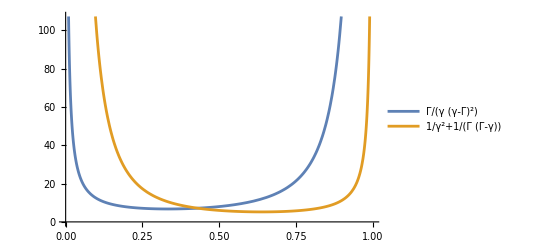

```mathematica
Plot[{Γ^2 QFIr,Γ^2 guessr},
{r,0,1},
PlotLegends->{QFI, guess}]
```

```mathematica
Γ/(γ (γ-Γ)^2)(2σ)^2/.γ->σ^2//Simplify
```

(4 Γ)/((Γ-σ^2)^2)

```mathematica
Clear[q]
q[n]:=p[n]/.γ->σ^2
QFI=Sum[D[q[n],σ]^2/q[n],{n,0,∞}]//FullSimplify
QFIr=QFI/.σ^2->r Γ//FullSimplify
```

(4 Γ)/((Γ-σ^2)^2)

4/((-1+r)^2 Γ)

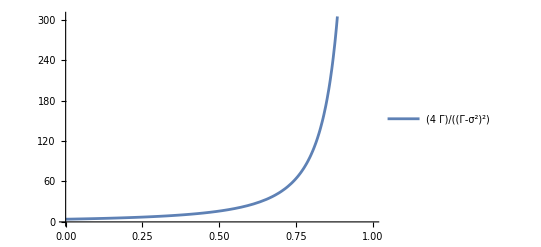

```mathematica
Plot[{Γ QFIr},
{r,0,1},
PlotLegends->{QFI,}]
```

```mathematica
Solve[D[T/(t+τ)IQ[t],t]==0,t]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[-(T IQ[t])/(t+τ)^2+(T IQ'[t])/(t+τ)==0,t]

Two-outcome measurement

```mathematica
pk1=Sum[ p[n],{n,0,k}]//FullSimplify
pk2=Sum[ p[n],{n,k+1,∞}]//FullSimplify
CFI=D[pk1,γ]^2/pk1+D[pk2,γ]^2/pk2//FullSimplify
(*checking Matteo's solution*)
CFI/.k->0//FullSimplify

CFI1=(CFI/.γ->ϵ Γ//FullSimplify)/.(1/ϵ)^k->1/ϵ^k//Together
%/.{-1+ϵ^(1+k)->-1,ϵ^(-1+k)->γ^(-1+k)/Γ^(-1+k)}//Together
```

1-(γ/Γ)^(1+k)

(γ/Γ)^(1+k)

(1+k)^2/(γ (-γ+Γ (Γ/γ)^k))

1/(γ (-γ+Γ))

-((1+k)^2 ϵ^(-1+k))/(Γ^2 (-1+ϵ^(1+k)))

(1+k)^2 γ^(-1+k) Γ^(-1-k)

Three-outcome measurement

```mathematica
pk0=Sum[ p[n],{n,0,k-1}]//FullSimplify
pk1= p[k]//FullSimplify
pk2=Sum[ p[n],{n,k+1,∞}]//FullSimplify
CFI=D[pk0,γ]^2/pk0+D[pk1,γ]^2/pk1+D[pk2,γ]^2/pk2//FullSimplify;
CFI=CFI/.{(γ/Γ)^k->γ^k/Γ^k,(γ/Γ^2)^k->γ^k/Γ^(2k)}//Together//FullSimplify

(*checking Matteo's solution*)
CFI0=-k^2/(γ^2((γ/Γ)^k-1))-k^2/γ^2-(γ/Γ)^k/(γ(γ-Γ));
CFI0==CFI//FullSimplify

(*expansion*)
CFI1=CFI/.γ->ϵ Γ//FullSimplify
CFI12=Γ^2/ϵ^(-2+k)CFI1
ϵ^(-2+k)/Γ^2 Series[CFI12,{ϵ,0,0}]//FullSimplify
Normal[%]/.ϵ->γ/Γ//FullSimplify
```

1-(γ/Γ)^k

γ^k Γ^(-1-k) (-γ+Γ)

(γ/Γ)^(1+k)

γ^(-2+k) (-(γ Γ^-k)/(γ-Γ)+k^2/(-γ^k+Γ^k))

True

(ϵ^(-2+k) (-ϵ/(-1+ϵ)-k^2/(-1+ϵ^k)))/Γ^2

-ϵ/(-1+ϵ)-k^2/(-1+ϵ^k)

(ϵ^(-2+k) (-k^2/(-1+ϵ^k)+O[ϵ]^1))/Γ^2

(k^2 γ^(-2+k))/(-γ^k+Γ^k)

SMSV

```mathematica
addToGlobalAssumptions[{γ>0,Γ>0,Γ>γ,t>0,r>0}]
Σ vac=1/2 IdentityMatrix[2];
Σ SMSV=1/2({{Exp[-2r], 0}, {0, Exp[2r]}});
```

```mathematica
(*Using ChatGPT's solution to the CM evolution*)
κ=Γ-γ;
n∞=γ/κ;
Σ t0=Σ SMSV;
Σ t∞=(1/2+n∞)IdentityMatrix[2];
Σ t1=Exp[-κ t]Σ t0+(1-Exp[-κ t])Σ t∞;
```

```mathematica
Block[{Σ=Σ t1/.γ->θ^2},
γ purity=FullSimplify[1/(√Det[2 Σ])];
QFI SMSV=FullSimplifyTimeConstrained[Tr[MatrixPower[Inverse[Σ].D[Σ, θ],2]]/(2 (1+(γ purity)^2))+(2 (D[γ purity, θ])^2)/(1-(γ purity)^4)];
QFI SMSV=QFI SMSV/.θ->Sqrt[γ];
(*purity and QFI of SMSV are verbose, but perhaps there is a small γ/Γ expansion?*)
]
```

FullSimplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

General::stop: Further output of FullSimplify::time will be suppressed during this calculation.

FullSimplify::gtime: Returning the simplest form found in the allowed time of 10. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
(*QFI SMSV HE=Limit[QFI SMSV,r->∞,PerformanceGoal->"Speed"]*)
```

TMSV

```mathematica
Σ vac=1/2 IdentityMatrix[4];
Σ TMSV=1/2({{Cosh[2r], 0, Sinh[2r], 0}, {0, Cosh[2r], 0, -Sinh[2r]}, {Sinh[2r], 0, Cosh[2r], 0}, {0, -Sinh[2r], 0, Cosh[2r]}});
```

```mathematica
(*(*If loss/gain acts on both modes*)
Σ t0=Σ TMSV;
Σ t∞=(1/2+n∞)IdentityMatrix[4];
Σ t1=Exp[-k t]Σ t0+(1-Exp[-k t])Σ t∞;*)
```

```mathematica
(*If loss/gain acts only on the first mode*)
k=G-g;
n∞=g/k;
Σ t0=Σ TMSV;
Mevo=DiagonalMatrix[{Exp[-k t/2],Exp[-k t/2],1,1}];
Nevo=(1-Exp[-k t])(1/2+n∞)DiagonalMatrix[{1,1,0,0}];
Σ t1=Mevo.Σ t0.Mevoᵀ+Nevo;
```

```mathematica
Σ t1//MatrixForm
```

((1-ⅇ^((g-G) t)) (1/2+g/(-g+G))+1/2 ⅇ^((g-G) t) Cosh[2 r] | 0 | 1/2 ⅇ^(1/2 (g-G) t) Sinh[2 r] | 0
0 | (1-ⅇ^((g-G) t)) (1/2+g/(-g+G))+1/2 ⅇ^((g-G) t) Cosh[2 r] | 0 | -1/2 ⅇ^(1/2 (g-G) t) Sinh[2 r]
1/2 ⅇ^(1/2 (g-G) t) Sinh[2 r] | 0 | 1/2 Cosh[2 r] | 0
0 | -1/2 ⅇ^(1/2 (g-G) t) Sinh[2 r] | 0 | 1/2 Cosh[2 r])

```mathematica
Block[{Σtmsv=Σ t1/.g->s^2},
μvec=({{0}, {0}, {0}, {0}});
QFI TMSV=Gaussian QFI Monras13[<|Σ->Σtmsv,analytic->True,μvec->μvec,θ->s,print->False,return->True,timeConstrained->True|>];
QFI TMSV=QFI TMSV/.s->Sqrt[g];
]
(*185.4 MB (down to 152.6 with assumptions. 85 MB with correct channel) of expression results, let's see if we can even export it to python;
At this size of analytic result, the difference to numerics is negligible unless we can take limits etc.*)
```

Save and load TMSV QFI

```mathematica
file tmsv=dir<>"tmsv_qfi.mx";
```

```mathematica
Put[QFI TMSV,file tmsv]
```

```mathematica
QFI TMSV1=Get[file tmsv];
```

```mathematica
QFI TMSV1
```

Export formulae to Python for plotting

```mathematica
toPythonTranslation = {γ->g,Γ->G};
```

```mathematica
Module[{path,nb},
path="/home/james/Code/pleasantpheasant/mathematica/ExportToPython.nb";
nb=NotebookOpen[path,CellContext->"Global`",Visible->False];
NotebookEvaluate[nb,InsertResults->False];
NotebookClose[nb];
];
Export[dir<>"../python_source/_QFI_SMSV_raw.py",QFI SMSV//TrigToExp//#/.toPythonTranslation&//ToPython,"Text"];
```

```mathematica
Module[{path,nb},
path="/home/james/Code/pleasantpheasant/mathematica/ExportToPython.nb";
nb=NotebookOpen[path,CellContext->"Global`",Visible->False];
NotebookEvaluate[nb,InsertResults->False];
NotebookClose[nb];
];
Export[dir<>"../python_source/_QFI_TMSV_raw.py",QFI TMSV//TrigToExp//#/.toPythonTranslation&//ToPython,"Text"];
(*took a while to export and created 200k (136k with assumptions. 126k with correct channel) lines of code, silly; TODO: fix this to export less but will need to at least initially simplify the expression a little.*)
```

Approx TMSV

```mathematica
Σ vac=1/2 IdentityMatrix[4];
Σ TMSV=1/2({{Cosh[2r], 0, Sinh[2r], 0}, {0, Cosh[2r], 0, -Sinh[2r]}, {Sinh[2r], 0, Cosh[2r], 0}, {0, -Sinh[2r], 0, Cosh[2r]}});
```

```mathematica
(*If loss/gain acts only on the first mode*)
k=G-g;
n∞=g/k;
Σ t0=Σ TMSV;
Mevo=DiagonalMatrix[{Exp[-k t/2],Exp[-k t/2],1,1}];
Nevo=(1-Exp[-k t])(1/2+n∞)DiagonalMatrix[{1,1,0,0}];
Σ t1=Mevo.Σ t0.Mevoᵀ+Nevo;
```

```mathematica
Σ t1//MatrixForm
```

((1-ⅇ^((g-G) t)) (1/2+g/(-g+G))+1/2 ⅇ^((g-G) t) Cosh[2 r] | 0 | 1/2 ⅇ^(1/2 (g-G) t) Sinh[2 r] | 0
0 | (1-ⅇ^((g-G) t)) (1/2+g/(-g+G))+1/2 ⅇ^((g-G) t) Cosh[2 r] | 0 | -1/2 ⅇ^(1/2 (g-G) t) Sinh[2 r]
1/2 ⅇ^(1/2 (g-G) t) Sinh[2 r] | 0 | 1/2 Cosh[2 r] | 0
0 | -1/2 ⅇ^(1/2 (g-G) t) Sinh[2 r] | 0 | 1/2 Cosh[2 r])

```mathematica
Σapprox=Normal[Series[Σ t1,{g,0,1}]]//FullSimplify;
Σapprox//MatrixForm
```

((ⅇ^(-G t) (-G+ⅇ^(G t) (2 g+G)-g (2+G t)+G (1+g t) Cosh[2 r]))/(2 G) | 0 | 1/4 ⅇ^(-(G t)/2) (2+g t) Sinh[2 r] | 0
0 | (ⅇ^(-G t) (-G+ⅇ^(G t) (2 g+G)-g (2+G t)+G (1+g t) Cosh[2 r]))/(2 G) | 0 | -1/4 ⅇ^(-(G t)/2) (2+g t) Sinh[2 r]
1/4 ⅇ^(-(G t)/2) (2+g t) Sinh[2 r] | 0 | 1/2 Cosh[2 r] | 0
0 | -1/4 ⅇ^(-(G t)/2) (2+g t) Sinh[2 r] | 0 | 1/2 Cosh[2 r])

```mathematica
Block[{Σtmsv=Σapprox/.g->s^2},
μvec=({{0}, {0}, {0}, {0}});
QFI TMSV=Gaussian QFI Monras13[<|Σ->Σtmsv,analytic->True,μvec->μvec,θ->s,print->False,return->True,timeConstrained->True|>];
QFI TMSV=QFI TMSV/.s->Sqrt[g];
]
(*87 MB: so no better than before.*)
```

```mathematica
QFIapprox=Normal[Series[QFI TMSV,{g,0,1}]];
(*A number of minutes and nothing returned.*)
```

$Aborted

Upper bound

```mathematica
addToGlobalAssumptions[{γ>0,Γ>0,Γ>γ,t>0,r>0}]
```

```mathematica
η[γ_]:=Exp[-(Γ-γ)t]
n∞[γ_]:=γ/(Γ-γ)
G[γ_]:=1+(1-η[γ])n∞[γ]//FullSimplify
ηPrime[γ_]:=η[γ]/G[γ]//FullSimplify
```

```mathematica
addToGlobalAssumptions[{Element[n,Integers],Element[k,Integers],Element[l,Integers],0<=k<=n,n>=0,l>=0,γ1>0,Γ>γ1,γ2>0,Γ>γ2,ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1>0,ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2>0}]
```

```mathematica
(*summand under the sqrt*)
expr=(1-ηPrime[γ1])^k ηPrime[γ1]^(n-k)(1-ηPrime[γ2])^k ηPrime[γ2]^(n-k)1/G[γ1]^(n-k+1)(1-1/G[γ1])^l 1/G[γ2]^(n-k+1)(1-1/G[γ2])^l; 
expr=expr//FullSimplify;
```

$Aborted

```mathematica
summand=Binomial[n-k+l,l]Binomial[n,k]Sqrt[expr]//FullSimplify;
```

```mathematica
sum1=Sum[summand,{l,0,∞}];
```

```mathematica
sum1=sum1//FullSimplify;
```

```mathematica
sum11=Sum[sum1,{k,0,n}];
```

```mathematica
sum11=sum11//FullSimplify;
```

```mathematica
(*Using that γ1<Γ and γ2<Γ such that ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1>0 and similar*)
sum11=sum11/.{(1/(ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1))^n->1/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1)^n),(1/(ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2))^n->1/((ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)^n)}//Simplify;
```

```mathematica
(*This (sum11) is the inner product, or at least the summand inside the sum over n, times p_n*)
file=dir<>"inner_product_summand.mx";
```

```mathematica
(*Put[sum11,file];*)
```

```mathematica
sum11=Get[file];
```

```mathematica
sum11/. n:>Style[n,Red,Bold]
```

ⅇ^(t Γ (1+n)) √(ⅇ^(t (γ1+γ2) n) ((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1)/((Γ-γ1) (Γ-γ2)))^(-1-2 n) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)^(-1-2 n)) (1-√(((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2)/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2))))^(-1-n) (1-ⅇ^(-t Γ) Γ √((ⅇ^(-t (γ1+γ2)) (ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) (ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2))/((Γ-γ1)^2 (Γ-γ2)^2)) (-1+√(((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2)/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)))))^n

```mathematica
ζ1=ⅇ^(t Γ)  √((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1)^-1 ((Γ-γ1) (Γ-γ2)) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)^-1)(1-√(((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2)/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2))))^-1;
ζ2n=ⅇ^(n t Γ) ⅇ^(1/2 n t (γ1+γ2)) (((Γ-γ1) (Γ-γ2))^n/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1)^n(ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)^n))  (1-√(((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2)/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2))))^-n (1-ⅇ^(-t Γ) Γ √((ⅇ^(-t (γ1+γ2)) (ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) (ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2))/((Γ-γ1)^2 (Γ-γ2)^2)) (-1+√(((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2)/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)))))^n;
((ζ1 ζ2n)/sum11)^2==1//FullSimplifyTimeConstrained
```

True

```mathematica
(*ζ2*)
y=ⅇ^(t Γ) ⅇ^(1/2 t (γ1+γ2)) (((Γ-γ1) (Γ-γ2))/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1)(ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)))  (1-√(((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2)/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2))))^-1 (1-ⅇ^(-t Γ) Γ √((ⅇ^(-t (γ1+γ2)) (ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) (ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2))/((Γ-γ1)^2 (Γ-γ2)^2)) (-1+√(((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2)/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)))));
(*((X y^n)/sum11)^2==1//FullSimplify*)
```

```mathematica
(*Manual simplification of y. TODO: Check that this is correct.*)
y1=ⅇ^(t Γ) ⅇ^(1/2 t (γ1+γ2)) (((Γ-γ1) (Γ-γ2))/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1)(ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)))  (Sqrt[(ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)]/(Sqrt[(ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)]-√((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2))+ⅇ^(-t Γ) Γ √((ⅇ^(-t (γ1+γ2)) (ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) (ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2))/((Γ-γ1)^2 (Γ-γ2)^2)) );
y2=ⅇ^(t Γ) ⅇ^(1/2 t (γ1+γ2)) (((Γ-γ1) (Γ-γ2))/((ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1)(ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)))  (Sqrt[(ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)]/(Sqrt[(ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)]-√((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2))+ⅇ^(-t Γ) Γ 1/((Γ-γ1)(Γ-γ2))Sqrt[ⅇ^(-t (γ1+γ2)) (ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2))]Sqrt[ (ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)]);
y3= 1/Sqrt[(ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1)(ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)]((ⅇ^(t Γ) ⅇ^(1/2 t (γ1+γ2))(Γ-γ1) (Γ-γ2))/(Sqrt[(ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1) (ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2)]-√((ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2)) γ1 γ2))+ Γ Sqrt[ (ⅇ^(t Γ)-ⅇ^(t γ1)) (ⅇ^(t Γ)-ⅇ^(t γ2))]);
```

```mathematica
addToGlobalAssumptions[{κ1>0,κ2>0,α1>0,α2>0,β1>0,β2>0}]
replRule={Γ-γ1->κ1,Γ-γ2->κ2,ⅇ^(t Γ)-ⅇ^(t γ1)->α1,ⅇ^(t Γ)-ⅇ^(t γ2)->α2,ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1->β1,ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2->β2};
{ζ1,ζ2n}/.replRule
```

{(ⅇ^(t Γ) √((κ1 κ2)/(β1 β2)))/(1-√((α1 α2 γ1 γ2)/(β1 β2))),ⅇ^(n t Γ+1/2 n t (γ1+γ2)) β1^-n β2^-n (1-√((α1 α2 γ1 γ2)/(β1 β2)))^-n (1-ⅇ^(-t Γ) Γ (-1+√((α1 α2 γ1 γ2)/(β1 β2))) √((ⅇ^(-t (γ1+γ2)) α1 α2 β1 β2)/(κ1^2 κ2^2)))^n (κ1 κ2)^n}

```mathematica
addToGlobalAssumptions[{κ1>0,κ2>0,α1>0,α2>0,β1>0,β2>0}]
replRule={Γ-γ1->κ1,Γ-γ2->κ2,ⅇ^(t Γ)-ⅇ^(t γ1)->α1,ⅇ^(t Γ)-ⅇ^(t γ2)->α2,ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1->β1,ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2->β2};
{ζ1,ζ2n}/.replRule//FullSimplifyTimeConstrained
```

FullSimplify::gtime: Returning the simplest form found in the allowed time of 10. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

{(ⅇ^(t Γ) √((κ1 κ2)/(β1 β2)))/(1-√((α1 α2 γ1 γ2)/(β1 β2))),ⅇ^(n t Γ+1/2 n t (γ1+γ2)) β1^-n β2^-n (1-√((α1 α2 γ1 γ2)/(β1 β2)))^-n (1-ⅇ^(-t Γ) Γ (-1+√((α1 α2 γ1 γ2)/(β1 β2))) √((ⅇ^(-t (γ1+γ2)) α1 α2 β1 β2)/(κ1^2 κ2^2)))^n (κ1 κ2)^n}

```mathematica
{(ⅇ^(t Γ) √(κ1 κ2))/(√(β1 β2)-√(α1 α2 γ1 γ2)),ⅇ^(n t Γ+1/2 n t (γ1+γ2)) β1^-n β2^-n (1-√((α1 α2 γ1 γ2)/(β1 β2)))^-n (1-ⅇ^(-t Γ) Γ (-1+√((α1 α2 γ1 γ2)/(β1 β2))) √((ⅇ^(-t (γ1+γ2)) α1 α2 β1 β2)/(κ1^2 κ2^2)))^n (κ1 κ2)^n};
{(ⅇ^(t Γ) √(κ1 κ2))/(√(β1 β2)-√(α1 α2 γ1 γ2)), β1^-n β2^-n ((κ1 κ2 √(β1 β2)ⅇ^(t Γ+1/2 t (γ1+γ2)))/(√(β1 β2)-√(α1 α2 γ1 γ2))+Γ  √(α1 α2 β1 β2))^n };
{(ⅇ^(t Γ) √(κ1 κ2))/(√(β1 β2)-√(α1 α2 γ1 γ2)),(1/(√(β1 β2)))^n((κ1 κ2 ⅇ^(t Γ+1/2 t (γ1+γ2)))/(√(β1 β2)-√(α1 α2 γ1 γ2))+Γ √(α1 α2))^n };
{(ⅇ^(t Γ) √(κ1 κ2))/(√(β1 β2)-√(α1 α2 γ1 γ2)),((ζ1 √(κ1 κ2)ⅇ^(1/2 t (γ1+γ2))+Γ √(α1 α2))/(√(β1 β2)))^n };
```

```mathematica
replRule//TableForm
```

Γ-γ1→κ1
Γ-γ2→κ2
ⅇ^(t Γ)-ⅇ^(t γ1)→α1
ⅇ^(t Γ)-ⅇ^(t γ2)→α2
ⅇ^(t Γ) Γ-ⅇ^(t γ1) γ1→β1
ⅇ^(t Γ) Γ-ⅇ^(t γ2) γ2→β2

Derivatives

```mathematica
(*2nd derivative of ip is sum over n of pn times deriv below*)
deriv=D[sum11,{γ1,2}]/.{γ1->γ,γ2->γ};
```

```mathematica
deriv/. n:>Style[n,Red,Bold];
```

```mathematica
addToGlobalAssumptions[{κ>0,α>0,β>0}]
replRule2={Γ-γ->κ,ⅇ^(t Γ)-ⅇ^(t γ)->α,ⅇ^(t Γ) Γ-ⅇ^(t γ) γ->β};
(deriv/.replRule2)/. n:>Style[n,Red,Bold];
```

```mathematica
replRule3={√((α^2 γ^2)/β^2)->(α γ)/β,√(β^2/(α^2 γ^2))->β/(α γ),1/(√((α^2 γ^2)/β^2))->β/(α γ),
√((ⅇ^(-2 t γ) α^2 β^2)/κ^4)->(ⅇ^(-t γ) α β)/κ^2,1/(√((ⅇ^(-2 t γ) α^2 β^2)/κ^4))->κ^2/(ⅇ^(-t γ) α β),
 √(ⅇ^(2 n t γ) β^(-1-2 n) (β/κ^2)^(-1-2 n))-> ⅇ^(n t γ) β^(-1-2 n)κ^(1+2 n),1/(√(ⅇ^(2 n t γ) β^(-1-2 n) (β/κ^2)^(-1-2 n)))->1/(ⅇ^(n t γ) β^(-1-2 n)κ^(1+2 n)),
 ((α^2 γ^2)/β^2)^(3/2)->(α^3 γ^3)/β^3,1/(((α^2 γ^2)/β^2)^(3/2))->1/((α^3 γ^3)/β^3),
((ⅇ^(-2 t γ) α^2 β^2)/κ^4)^(3/2)->(ⅇ^(-3 t γ) α^3 β^3)/κ^6,1/(((ⅇ^(-2 t γ) α^2 β^2)/κ^4)^(3/2))->1/((ⅇ^(-3 t γ) α^3 β^3)/κ^6),
(ⅇ^(2 n t γ) β^(-1-2 n) (β/κ^2)^(-1-2 n))^(3/2)-> ⅇ^(3n t γ) β^(-3-6 n)κ^(3+6 n),1/((ⅇ^(2 n t γ) β^(-1-2 n) (β/κ^2)^(-1-2 n))^(3/2))->1/(ⅇ^(3n t γ) β^(-3-6 n)κ^(3+6 n))
};
deriv2=(deriv/.replRule2)/.replRule3;
```

```mathematica
deriv2=FullSimplify[deriv2,TimeConstraint->10];
```

FullSimplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
Collect[deriv2,n]/. n:>Style[n,Red,Bold]
```

Coherent state: loss sensing and the Jacobian to gain sensing

```mathematica
Clear[η,n∞]
μ0=({{Sqrt[2]α}, {0}});
Σ0=1/2 IdentityMatrix[2];
Σ∞=(1/2+n∞)IdentityMatrix[2];

(*thermal loss channel*)
μ[t_]:=Sqrt[η]μ0
Σ[t_]:=η Σ0+(1-η)Σ∞

(*loss (more strictly, transmissivity) sensing*)
QFI coherent wrt η=Gaussian QFI[μ[t],Σ[t],η]//FullSimplify;
Collect[QFI coherent wrt η,α,FullSimplify]
```

(n∞)/((-1+n∞ (-1+η)) (-1+η))+α^2/(η-2 n∞ (-1+η) η)

```mathematica
(*noise sensing*)
QFI coherent wrt n∞=Gaussian QFI[μ[t],Σ[t],n∞]//FullSimplify;
Collect[QFI coherent wrt n∞,α,FullSimplify]
```

(-1+η)/(n∞ (-1+n∞ (-1+η)))

```mathematica
Clear[κ,n∞]
η=Exp[-κ t];

(*loss (more strictly, transmissivity) sensing*)
QFI coherent wrt κ=Gaussian QFI[μ[t],Σ[t],κ]//FullSimplify;
Collect[QFI coherent wrt κ,α,FullSimplify]
```

(n∞ t^2)/(n∞+ⅇ^(t κ) (-1-2 n∞+ⅇ^(t κ) (1+n∞)))+(t^2 α^2)/(-2 n∞+ⅇ^(t κ) (1+2 n∞))

```mathematica
(*gain sensing*)
Clear[Γ,γ]
κ=Γ-γ;
n∞=γ/κ;
QFI coherent wrt sqrtγ=Gaussian QFI[μ[t]/.γ->σ^2,Σ[t]/.γ->σ^2,σ]/.σ->Sqrt[γ]//FullSimplify;
Collect[QFI coherent wrt sqrtγ,α,FullSimplify]
```

(4 ⅇ^(t γ) t^2 α^2 γ (γ-Γ))/(2 ⅇ^(t γ) γ-ⅇ^(t Γ) (γ+Γ))+(4 (ⅇ^(t Γ) Γ-ⅇ^(t γ) (Γ+t γ (-γ+Γ)))^2)/((ⅇ^(t γ)-ⅇ^(t Γ)) (γ-Γ)^2 (ⅇ^(t γ) γ-ⅇ^(t Γ) Γ))

```mathematica
addToGlobalAssumptions[{γ>0,Γ>0,Γ>γ,t>0,r>0}]
Limit[QFI coherent wrt sqrtγ,t->∞]
Series[QFI coherent wrt sqrtγ,{t,0,1}]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(4 Γ)/(γ-Γ)^2

4 t+O[t]^2

```mathematica
Collect[QFI coherent wrt sqrtγ/.γ->ϵ Γ,α,FullSimplify]
Series[QFI coherent wrt sqrtγ/.γ->ϵ Γ,{ϵ,0,0}]
```

(4 ⅇ^(t Γ ϵ) t^2 α^2 Γ (-1+ϵ) ϵ)/(2 ⅇ^(t Γ ϵ) ϵ-ⅇ^(t Γ) (1+ϵ))+(4 (ⅇ^(t Γ)+ⅇ^(t Γ ϵ) (-1+t Γ (-1+ϵ) ϵ))^2)/((ⅇ^(t Γ)-ⅇ^(t Γ ϵ)) Γ (-1+ϵ)^2 (ⅇ^(t Γ)-ⅇ^(t Γ ϵ) ϵ))

(4 ⅇ^(-t Γ) (-1+ⅇ^(t Γ)))/Γ+O[ϵ]^1

```mathematica
toPythonTranslation = {γ->g,Γ->G,α->alpha};
Module[{path,nb},
path="/home/james/Code/pleasantpheasant/mathematica/ExportToPython.nb";
nb=NotebookOpen[path,CellContext->"Global`",Visible->False];
NotebookEvaluate[nb,InsertResults->False];
NotebookClose[nb];
];
Export[dir<>"../python_source/_QFI_coherent_raw.py",QFI coherent wrt sqrtγ//TrigToExp//#/.toPythonTranslation&//ToPython,"Text"];
```

```mathematica
(*finding the optimal coherent QFI for Matteo at small Nbar*)
Collect[QFI coherent wrt sqrtγ,α,FullSimplify]
Collect[QFI coherent wrt sqrtγ/.γ->ϵ Γ,α,FullSimplify]
x=Series[QFI coherent wrt sqrtγ/.γ->ϵ Γ,{ϵ,0,1}]//FullSimplify
x=Collect[Normal[x],{α,ϵ},FullSimplify]
x=x/.{ϵ->γ/Γ,α^2->n}
```

(4 ⅇ^(t γ) t^2 α^2 γ (γ-Γ))/(2 ⅇ^(t γ) γ-ⅇ^(t Γ) (γ+Γ))+(4 (ⅇ^(t Γ) Γ-ⅇ^(t γ) (Γ+t γ (-γ+Γ)))^2)/((ⅇ^(t γ)-ⅇ^(t Γ)) (γ-Γ)^2 (ⅇ^(t γ) γ-ⅇ^(t Γ) Γ))

(4 ⅇ^(t Γ ϵ) t^2 α^2 Γ (-1+ϵ) ϵ)/(2 ⅇ^(t Γ ϵ) ϵ-ⅇ^(t Γ) (1+ϵ))+(4 (ⅇ^(t Γ)+ⅇ^(t Γ ϵ) (-1+t Γ (-1+ϵ) ϵ))^2)/((ⅇ^(t Γ)-ⅇ^(t Γ ϵ)) Γ (-1+ϵ)^2 (ⅇ^(t Γ)-ⅇ^(t Γ ϵ) ϵ))

(4-4 ⅇ^(-t Γ))/Γ+(ⅇ^(-2 t Γ) (-4+4 ⅇ^(t Γ) (-1+2 ⅇ^(t Γ)+t Γ (-3+t α^2 Γ))) ϵ)/Γ+O[ϵ]^2

(4-4 ⅇ^(-t Γ))/Γ+4 ⅇ^(-t Γ) t^2 α^2 Γ ϵ+(4 ⅇ^(-t Γ) ϵ (-1-3 t Γ+Cosh[t Γ]+3 Sinh[t Γ]))/Γ

4 ⅇ^(-t Γ) n t^2 γ+(4-4 ⅇ^(-t Γ))/Γ+(4 ⅇ^(-t Γ) γ (-1-3 t Γ+Cosh[t Γ]+3 Sinh[t Γ]))/Γ^2

```mathematica
(*have to be careful about the steady state limit (order of limits)*)
Limit[x,t->∞]
Series[%,{γ,0,2}]
Limit[QFI coherent wrt sqrtγ,t->∞]
Series[%,{γ,0,2}]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(4 (2 γ+Γ))/Γ^2

4/Γ+(8 γ)/Γ^2+O[γ]^3

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(4 Γ)/(γ-Γ)^2

4/Γ+(8 γ)/Γ^2+(12 γ^2)/Γ^3+O[γ]^3

```mathematica
Reduce[D[x,t]==0,t]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[4 ⅇ^(-t Γ)+8 ⅇ^(-t Γ) n t γ-4 ⅇ^(-t Γ) n t^2 γ Γ-(4 ⅇ^(-t Γ) γ (-1-3 t Γ+Cosh[t Γ]+3 Sinh[t Γ]))/Γ+(4 ⅇ^(-t Γ) γ (-3 Γ+3 Γ Cosh[t Γ]+Γ Sinh[t Γ]))/Γ^2==0,t]

```mathematica
Series[D[x,t],{t,0,1}]//Normal//FullSimplify
```

4+4 t (γ+2 n γ-Γ)

```mathematica
addToGlobalAssumptions[{n>0}]
xx=4 ⅇ^(-t Γ) n t^2 γ+(4-4 ⅇ^(-t Γ))/Γ;
sol=Solve[D[xx,t]==0,t]//FullSimplify
xx/.sol//FullSimplify
4 ⅇ^(-t Γ) n t^2 γ/.sol//FullSimplify
```

{{t→(1+√(1+Γ/(n γ)))/Γ}}

{(ⅇ^(-1-√(1+Γ/(n γ))) (8 n γ+4 ⅇ^(1+√(1+Γ/(n γ))) Γ+8 √(n γ (n γ+Γ))))/Γ^2}

{(ⅇ^(-1-√(1+Γ/(n γ))) (8 n γ+4 Γ+8 √(n γ (n γ+Γ))))/Γ^2}

```mathematica
sol∞=t->Limit[t/.sol[[1,1]],n->∞]
xx/.sol∞
%//N
2.5904409515676594/2.1653645317858032
Sqrt[%]
2.59/2.17
Sqrt[%]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

t→2/Γ

(16 n γ)/(ⅇ^2 Γ^2)+(4-4/ⅇ^2)/Γ

(2.16536 n γ)/Γ^2+3.45866/Γ

1.19631

1.09376

1.19355

1.0925

```mathematica
(*finding the optimal coherent time numerically for Matteo's case, do this in python instead?*)
```

```mathematica
y=(4n γ t^2 E^(-Γ t))/(1-E^(-Γ t));
sol=Solve[D[y,t]==0,t]//FullSimplify
y/.sol//FullSimplify
sol//N
y/.%
```

{{t→(2+ProductLog[-2/ⅇ^2])/Γ}}

{-(4 n γ ProductLog[-2/ⅇ^2] (2+ProductLog[-2/ⅇ^2]))/Γ^2}

{{t→1.59362/Γ}}

{(2.59044 n γ)/Γ^2}

Scenario 2

```mathematica
(*Scenario 2 (instead of Scenario 1 above)*)
Clear[Γ,γ,κ,η,n∞]
(*κ is Γ'*)
η=Exp[-κ t];
n∞=γ/κ;
μ[t]//FullSimplify//MatrixForm
Σ[t]//FullSimplify//MatrixForm
Gaussian QFI[μ[t]/.γ->σ^2,Σ[t]/.γ->σ^2,σ]/.σ->Sqrt[γ]//FullSimplify//Together//FullSimplify
```

(√2 √(ⅇ^(-t κ)) α
0)

((2 γ-2 ⅇ^(-t κ) γ+κ)/(2 κ) | 0
0 | (2 γ-2 ⅇ^(-t κ) γ+κ)/(2 κ))

(4 (-1+ⅇ^(t κ)))/(-γ+ⅇ^(t κ) (γ+κ))

```mathematica
(*Scenario 2, SMSV*)
μ1=({{0}, {0}});
Σ1=DiagonalMatrix[{1/2 E^(-2r),1/2 E^(2r)}];
μ11[t_]:=Sqrt[η]μ1
Σ11[t_]:=η Σ1+(1-η)Σ∞
μ11[t]//FullSimplify//MatrixForm
Σ11[t]//FullSimplify//MatrixForm
smsv=Gaussian QFI[μ11[t]/.γ->σ^2,Σ11[t]/.γ->σ^2,σ]/.σ->Sqrt[γ]//FullSimplify//Together//FullSimplify
addToGlobalAssumptions[{γ>0,Γ>0,Γ>γ,t>0,r>0,κ>0}]
Limit[smsv,r->∞]
```

(0
0)

(1/2 ⅇ^(-2 r-t κ)+(1-ⅇ^(-t κ)) (1/2+γ/κ) | 0
0 | (ⅇ^(-t κ) (ⅇ^(2 r) κ+(-1+ⅇ^(t κ)) (2 γ+κ)))/(2 κ))

(8 (-1+ⅇ^(t κ)) γ (κ^2+ⅇ^(8 r) κ^2+2 ⅇ^(2 r) (-1+ⅇ^(t κ)) κ (2 γ+κ)+2 ⅇ^(6 r) (-1+ⅇ^(t κ)) κ (2 γ+κ)+2 ⅇ^(4 r) ((2 γ+κ)^2-2 ⅇ^(t κ) (2 γ+κ)^2+2 ⅇ^(2 t κ) (2 γ^2+2 γ κ+κ^2))))/((4 ⅇ^(2 r+t κ) γ (γ+κ)+κ (2 γ+κ)+ⅇ^(4 r) κ (2 γ+κ)-2 ⅇ^(2 r) (2 γ^2+2 γ κ+κ^2)) (-κ (2 γ+κ)-ⅇ^(4 r) κ (2 γ+κ)+ⅇ^(t κ) κ (2 γ+κ)+ⅇ^(4 r+t κ) κ (2 γ+κ)-2 ⅇ^(2 r+t κ) (2 γ+κ)^2+2 ⅇ^(2 r) (2 γ^2+2 γ κ+κ^2)+2 ⅇ^(2 (r+t κ)) (2 γ^2+2 γ κ+κ^2)))

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(8 γ)/(2 γ+κ)^2

```mathematica
(*Upper bound, Scenario 2*)
(*(1-E^(-κ t))^2(4γ)/κ^2 4/(1-E^(-κ t)+(1-E^(-κ t))^2 γ^2/κ^2)//FullSimplify*)
η1=1-E^(-κ t);
σ1=Sqrt[(1-E^(-κ t))γ/κ]//FullSimplify
4/(η1+σ1^2)//FullSimplify
deriv=D[σ1/.γ->s^2,s]/.s->Sqrt[γ]//FullSimplify
deriv^2//FullSimplify
qfiUB=deriv^2 4/(η1+σ1^2)//FullSimplify
```

√((γ-ⅇ^(-t κ) γ)/κ)

(4 ⅇ^(t κ) κ)/((-1+ⅇ^(t κ)) (γ+κ))

ⅇ^(-(t κ)/2) √((-1+ⅇ^(t κ))/κ)

(1-ⅇ^(-t κ))/κ

4/(γ+κ)

Quantum radar

```mathematica
D[(Nb/(Nb+1))^n,Nb]==(1/(Nb+1))^2 n(Nb/(Nb+1))^(n-1)//FullSimplify
```

True

```mathematica
(1/(Nb+1))^4 Sum[n^2(Nb/(Nb+1))^(n-2),{n,0,∞}]
```

(1+2 Nb)/(Nb (1+Nb))

```mathematica
p[n_]:=(Nb/(Nb+1))^n
Sum[D[p[n],Nb]^2/p[n],{n,0,∞}]
```

(1+2 Nb)/(Nb (1+Nb))

```mathematica
Hc=(4 Ns)/(1+2Nb);
Htms=(4 Ns)/(1+Nb)1/(1+Ns/(1+Ns)Nb/(1+Nb));
Hq=Min[(4Ns)/(1+Nb),(2Ns+1)/Nb];
```

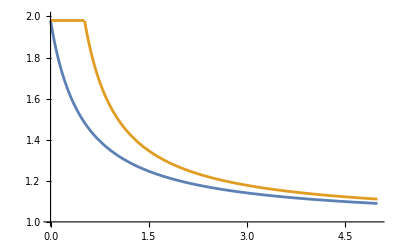

```mathematica
Block[{Nb=50},
Plot[{Htms/Hc,Hq/Hc},{Ns,0,5},PlotRange->{1,2}]]
```

```mathematica
κ=Γ-γ;
Nb=γ/κ;
η=Exp[-κ t];
ηdSqr=D[η/.γ->s^2,s]^2/.s->Sqrt[γ]//FullSimplify
NbdSqr=D[Nb/.γ->s^2,s]^2/.s->Sqrt[γ]//FullSimplify
```

4 ⅇ^(2 t (γ-Γ)) t^2 γ

(4 γ Γ^2)/(γ-Γ)^4

```mathematica
QFIlim=ηdSqr H +NbdSqr (1+2 Nb)/(Nb(1+Nb))//FullSimplify
```

4 ⅇ^(2 t (γ-Γ)) H t^2 γ+(4 Γ (γ+Γ))/(-γ+Γ)^3

```mathematica
QFIlimC=QFIlim/.H->Hc//FullSimplify
```

-(16 ⅇ^(2 t (γ-Γ)) Ns t^2 γ (γ-Γ))/(γ+Γ)+(4 Γ (γ+Γ))/(-γ+Γ)^3

```mathematica
QFIlimTms=QFIlim/.H->Htms//FullSimplify
```

(4 Γ (γ+Γ))/(-γ+Γ)^3-(16 ⅇ^(2 t (γ-Γ)) Ns (1+Ns) t^2 γ (γ-Γ))/(Γ+Ns (γ+Γ))

```mathematica
QFIlimQ=QFIlim/.H->Hq//FullSimplify
```

(4 Γ (γ+Γ))/(-γ+Γ)^3+4 ⅇ^(2 t (γ-Γ)) t^2 γ Min[Ns (4-(4 γ)/Γ),((1+2 Ns) (-γ+Γ))/γ]

```mathematica
Htms/Hc//FullSimplify
```

1+γ/(Γ+Ns (γ+Γ))

```mathematica
(*TODO: need to take the long time limit of the derivatives here, will kill the first term?*)
Block[{Γ=0.2,γ=0.01},
Plot[{QFIlimTms/QFIlimC,QFIlimQ/QFIlimC},{Ns,0,5},PlotRange->{1,2}]]
```

-Graphics-

Small parameter expansion

```mathematica
κ=Γ-γ;
n∞=γ/κ;
η=Exp[-κ t];
G=1+(1-η)n∞;
ηPrime=η/G;

{κ,n∞,η,G,ηPrime}
%//FullSimplify
```

{-γ+Γ,γ/(-γ+Γ),ⅇ^(t (γ-Γ)),1+((1-ⅇ^(t (γ-Γ))) γ)/(-γ+Γ),ⅇ^(t (γ-Γ))/(1+((1-ⅇ^(t (γ-Γ))) γ)/(-γ+Γ))}

{-γ+Γ,γ/(-γ+Γ),ⅇ^(t (γ-Γ)),(ⅇ^(t (γ-Γ)) γ-Γ)/(γ-Γ),(ⅇ^(t γ) (γ-Γ))/(ⅇ^(t γ) γ-ⅇ^(t Γ) Γ)}

```mathematica
x1=Series[ηPrime,{γ,0,1}]//FullSimplify
x2=Series[G,{γ,0,1}]//FullSimplify
```

ⅇ^(-t Γ)+(ⅇ^(-2 t Γ) (1+ⅇ^(t Γ) (-1+t Γ)) γ)/Γ+O[γ]^2

1+((1-ⅇ^(-t Γ)) γ)/Γ+O[γ]^2

```mathematica
ηPrime/.γ->ϵ/t//FullSimplify;
Series[%,{ϵ,0,1}]//FullSimplify
Normal[%]/.ϵ->γ t//FullSimplify
Normal[x1]==%//FullSimplify
```

ⅇ^(-t Γ)+(ⅇ^(-2 t Γ) (1+ⅇ^(t Γ) (-1+t Γ)) ϵ)/(t Γ)+O[ϵ]^2

(ⅇ^(-2 t Γ) (γ+ⅇ^(t Γ) (Γ+γ (-1+t Γ))))/Γ

True

```mathematica
G/.γ->ϵ/t//FullSimplify;
Series[%,{ϵ,0,1}]//FullSimplify
Normal[%]/.ϵ->γ t//FullSimplify
Normal[x2]==%//FullSimplify
```

1+((1-ⅇ^(-t Γ)) ϵ)/(t Γ)+O[ϵ]^2

(γ-ⅇ^(-t Γ) γ+Γ)/Γ

True

Quntao

```mathematica
(*Eq11*)
addToGlobalAssumptions[{Subscript[σ, 1]>0}]
QFIub=1/(Subscript[n, B](Subscript[n, B]+1))+(κ Subscript[n, S](2 Subscript[n, B]-κ+1))/(Subscript[n, B](Subscript[n, B]+1)^2(Subscript[n, B]-κ+1))//Together//FullSimplify//Together
QFIstoch=QFIub/.{κ->Subscript[η, 1],Subscript[n, B]->Subscript[σ, 1]^2,Subscript[n, S]->n}//FullSimplify
(*still need the QFI change of variables*)
QFIstochWrtSigma1=4 Subscript[σ, 1]^2 QFIstoch//FullSimplify
```

(1-κ+2 n_B-κ n_B+n_B^2+κ n_S-κ^2 n_S+2 κ n_B n_S)/(n_B (1+n_B)^2 (1-κ+n_B))

(-n η_1^2+(1+σ_1^2)^2+η_1 (-1+n+(-1+2 n) σ_1^2))/((1-η_1+σ_1^2) (σ_1+σ_1^3)^2)

(4 (-n η_1^2+(1+σ_1^2)^2+η_1 (-1+n+(-1+2 n) σ_1^2)))/((1+σ_1^2)^2 (1-η_1+σ_1^2))

TMSV - Scenario 2

```mathematica
Σ vac=1/2 IdentityMatrix[4];
Σ TMSV=1/2({{Cosh[2r], 0, Sinh[2r], 0}, {0, Cosh[2r], 0, -Sinh[2r]}, {Sinh[2r], 0, Cosh[2r], 0}, {0, -Sinh[2r], 0, Cosh[2r]}});
```

```mathematica
(*If loss/gain acts only on the first mode*)
κ=G-γ;(*can't call it Γ because that is used in the Gaussian QFI calculator*)
η=E^(-κ t);
nth=γ/κ;
Mevo=DiagonalMatrix[{E^(-κ t/2),E^(-κ t/2),1,1}];
Nevo=(1-η)(1/2+nth)DiagonalMatrix[{1,1,0,0}];
Σfinal=Mevo.Σ TMSV.Mevoᵀ+Nevo;
```

```mathematica
Σfinal//MatrixForm
```

((1-ⅇ^(t (-G+γ))) (1/2+γ/(G-γ))+1/2 ⅇ^(t (-G+γ)) Cosh[2 r] | 0 | 1/2 ⅇ^(1/2 t (-G+γ)) Sinh[2 r] | 0
0 | (1-ⅇ^(t (-G+γ))) (1/2+γ/(G-γ))+1/2 ⅇ^(t (-G+γ)) Cosh[2 r] | 0 | -1/2 ⅇ^(1/2 t (-G+γ)) Sinh[2 r]
1/2 ⅇ^(1/2 t (-G+γ)) Sinh[2 r] | 0 | 1/2 Cosh[2 r] | 0
0 | -1/2 ⅇ^(1/2 t (-G+γ)) Sinh[2 r] | 0 | 1/2 Cosh[2 r])

```mathematica
Block[{Σ1=Σfinal/.γ->s^2},
μvec=({{0}, {0}, {0}, {0}});
QFI TMSV=Gaussian QFI Monras13[<|Σ->Σ1,analytic->True,μvec->μvec,θ->s,print->False,return->True,timeConstrained->True|>];
QFI TMSV=QFI TMSV/.s->Sqrt[γ];
]
```

```mathematica
QFI TMSV
```

```mathematica
qfi=(1-E^(-G t))/((t+τ)((1-E^(-G t))nbar+1));
dqfi=D[qfi,t]//FullSimplify
Reduce[dqfi==0,t]
```

-(nbar+ⅇ^(2 G t) (1+nbar)-ⅇ^(G t) (1+2 nbar+G (t+τ)))/((nbar-ⅇ^(G t) (1+nbar))^2 (t+τ)^2)

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-(nbar+ⅇ^(2 G t) (1+nbar)-ⅇ^(G t) (1+2 nbar+G (t+τ)))/((nbar-ⅇ^(G t) (1+nbar))^2 (t+τ)^2)==0,t]

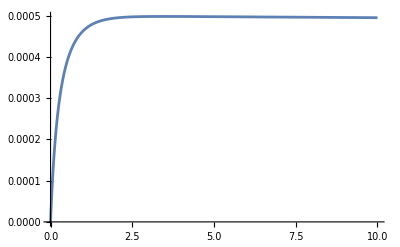

```mathematica
Block[{τ=1000,G=2,nbar=1},
Plot[qfi,{t,0,10},PlotRange->{0,All}]
]
```

```mathematica
Reduce[D[(1-E^(-G t))/(t((1-E^(-G t))nbar+1)),t]==0,t]
Reduce[D[(1-E^(-G t))/(τ((1-E^(-G t))nbar+1)),t]==0,t]
D[(1-E^(-G t))/(τ((1-E^(-G t))nbar+1)),t]
%//FullSimplify
%/.t->0
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-(1-ⅇ^(-G t))/((1+(1-ⅇ^(-G t)) nbar) t^2)-(ⅇ^(-G t) (1-ⅇ^(-G t)) G nbar)/((1+(1-ⅇ^(-G t)) nbar)^2 t)+(ⅇ^(-G t) G)/((1+(1-ⅇ^(-G t)) nbar) t)==0,t]

τ≠0&&G==0

-(ⅇ^(-G t) (1-ⅇ^(-G t)) G nbar)/((1+(1-ⅇ^(-G t)) nbar)^2 τ)+(ⅇ^(-G t) G)/((1+(1-ⅇ^(-G t)) nbar) τ)

(ⅇ^(G t) G)/((nbar-ⅇ^(G t) (1+nbar))^2 τ)

G/τ

```mathematica
qfi=(4(nbar+1)t)/((t+τ)(G t nbar+1))//FullSimplify
sol=FullSimplify[Solve[D[qfi,t]==0,t],Assumptions->{t>0,nbar>0,τ>0,G>0}]
qfiopt=qfi/.sol[[2]]//FullSimplify
FullSimplify[qfiopt==(4 (1+nbar))/(1+G nbar τ+2 √(G nbar τ)),Assumptions->{t>0,nbar>0,τ>0,G>0}]
FullSimplify[qfiopt==(4 (1+nbar))/(1+√(G nbar τ) )^2,Assumptions->{t>0,nbar>0,τ>0,G>0}]
```

(4 (1+nbar) t)/((1+G nbar t) (t+τ))

{{t→-τ/(√(G nbar τ))},{t→1/(√((G nbar)/τ))}}

(4 (1+nbar))/(1+G nbar τ+2 √((G nbar)/τ) τ)

True

True

```mathematica
G+nbar((1-eta2)G+G-1)/.{G->1+nth (1-eta),eta2->eta/(1+nth (1-eta))}//FullSimplify
```

1+nth-eta nth-(-1+eta) nbar (1+2 nth)

Loss estimation

```mathematica
θ1=ArcCos[Sqrt[η/(1+(1-η)Subscript[n, th])]];
θ2=ArcCosh[Sqrt[1+(1-η)Subscript[n, th]]];
```

```mathematica
D[θ1,η]//FullSimplify
D[θ2,η]//FullSimplify
```

(√(-((-1+η) η (1+n_th))/(-1+(-1+η) n_th)^2))/(2 (-1+η) η)

-n_th/(2 √(1-(-1+η) n_th) √(-1+√(1+n_th-η n_th)) √(1+√(1+n_th-η n_th)))

```mathematica
D[θ1,η]^2//FullSimplify
D[θ2,η]^2//FullSimplify
```

-(1+n_th)/(4 (-1+η) η (-1+(-1+η) n_th)^2)

n_th/(4 (-1+η) (-1+(-1+η) n_th))

```mathematica
(*denominator*)
denominator=Cosh[θ2]^2+Nbar(Sin[θ1]^2 Cosh[θ2]^2+Sinh[θ2]^2)//FullSimplify
Collect[%,Nbar,FullSimplify]
```

1+Nbar-Nbar η-(1+2 Nbar) (-1+η) n_th

1-(-1+η) n_th-Nbar (-1+η) (1+2 n_th)

```mathematica
(*full expression*)
(4 D[θ2,η]^2 Cosh[θ2]^2+4 Nbar^2(D[θ1,η]Sin[θ1]Cosh[θ2]-D[θ2,η]Cos[θ1]Sinh[θ2])^2+4 Nbar(D[θ1,η]^2 Cosh[θ2]^2+D[θ2,η]^2 Cosh[2 θ2]))/(Cosh[θ2]^2+Nbar(Sin[θ1]^2 Cosh[θ2]^2+Sinh[θ2]^2))//FullSimplify
```

-((η n_th^2 (-1+(-1+η) n_th)^2+Nbar n_th (-1+(-1+η) n_th)^2 (1+2 η n_th)+Nbar^2 (1+√(1+n_th-η n_th)) ((1+n_th) √(-1+√(1+n_th-η n_th))-η n_th √((-1+√(1+n_th-η n_th))/(1+√(1+n_th-η n_th))) √(1+√(1+n_th-η n_th)))^2)/((-1+η) η n_th (-1+(-1+η) n_th)^2 (1+Nbar-Nbar η-(1+2 Nbar) (-1+η) n_th)))

```mathematica
(*bar N^2 term*)
quadCoeff=4(D[θ1,η]Sin[θ1]Cosh[θ2]-D[θ2,η]Cos[θ1]Sinh[θ2])^2//FullSimplify
(*bar N term*)
linCoeff=4(D[θ1,η]^2 Cosh[θ2]^2+D[θ2,η]^2 Cosh[2 θ2])//FullSimplify//Factor
(*constant term*)
constCoeff=4 D[θ2,η]^2 Cosh[θ2]^2//FullSimplify
```

1/η

-(1+2 η n_th)/((-1+η) η)

n_th/(1-η)

```mathematica
(*numerator*)
numerator=constCoeff+Nbar^2 quadCoeff+Nbar linCoeff//FullSimplify
ecqfiUB=numerator/denominator//FullSimplify
ecqfiUB2=Collect[Numerator[ecqfiUB],Nbar,FullSimplify]/Collect[Denominator[ecqfiUB],Nbar,FullSimplify]
ecqfiUB==ecqfiUB2//FullSimplify
```

-(Nbar (1+Nbar-Nbar η)+(η+2 Nbar η) n_th)/((-1+η) η)

(Nbar (1+Nbar-Nbar η)+(η+2 Nbar η) n_th)/((-1+η) η (-1+Nbar (-1+η)+(1+2 Nbar) (-1+η) n_th))

(Nbar^2 (1-η)+η n_th+Nbar (1+2 η n_th))/(Nbar (-1+η)^2 η (1+2 n_th)+(-1+η) η (-1+(-1+η) n_th))

True

```mathematica
(*Sanz17 Eq.6*)
qfi=(4Ns)/(1+Nb)1/(1+Ns/(1+Ns)Nb/(1+Nb))//FullSimplify
Numerator[Together[qfi]]/Collect[Denominator[Together[qfi]],Ns]
%==qfi//Simplify
```

(4 Ns (1+Ns))/(1+Nb+Ns+2 Nb Ns)

(4 Ns (1+Ns))/(1+Nb+(1+2 Nb) Ns)

True

```mathematica
qfi=(Nbar^2 (1-η)+η Subscript[n, th]+Nbar (1+2 η Subscript[n, th]))/(Nbar (-1+η)^2 η (1+2 Subscript[n, th])+(-1+η) η (-1+(-1+η) Subscript[n, th]));
qfi2=qfi/.{η->E^(-κ t),Subscript[n, th]->γ/κ}//FullSimplify
```

(ⅇ^(2 t κ) (γ+2 Nbar γ+Nbar (-Nbar+ⅇ^(t κ) (1+Nbar)) κ))/((-1+ⅇ^(t κ)) ((-1+ⅇ^(t κ)) (1+2 Nbar) γ-Nbar κ+ⅇ^(t κ) (1+Nbar) κ))

```mathematica
addToGlobalAssumptions[{Nbar>0,γ>0,t>=0,κ>0}]
```

```mathematica
sol=Solve[D[qfi2,t]==0,t]
```

{{t→ConditionalExpression[1/κ Log[Root[2 γ^2+8 Nbar γ^2+8 Nbar^2 γ^2+2 Nbar γ κ+2 Nbar^2 γ κ-4 Nbar^3 γ κ-2 Nbar^3 κ^2+(-2 γ^2-8 Nbar γ^2-8 Nbar^2 γ^2-γ κ-Nbar γ κ+7 Nbar^2 γ κ+10 Nbar^3 γ κ+4 Nbar^2 κ^2+5 Nbar^3 κ^2) #1+(-4 Nbar γ κ-12 Nbar^2 γ κ-8 Nbar^3 γ κ-2 Nbar κ^2-6 Nbar^2 κ^2-4 Nbar^3 κ^2) #1^2+(Nbar γ κ+3 Nbar^2 γ κ+2 Nbar^3 γ κ+Nbar κ^2+2 Nbar^2 κ^2+Nbar^3 κ^2) #1^3&,3]], ]}}

```mathematica
sol=sol//FullSimplify
```

{{t→ConditionalExpression[1/κ Log[Root[2 γ^2+8 Nbar γ^2+8 Nbar^2 γ^2+2 Nbar γ κ+2 Nbar^2 γ κ-4 Nbar^3 γ κ-2 Nbar^3 κ^2+(-2 γ^2-8 Nbar γ^2-8 Nbar^2 γ^2-γ κ-Nbar γ κ+7 Nbar^2 γ κ+10 Nbar^3 γ κ+4 Nbar^2 κ^2+5 Nbar^3 κ^2) #1+(-4 Nbar γ κ-12 Nbar^2 γ κ-8 Nbar^3 γ κ-2 Nbar κ^2-6 Nbar^2 κ^2-4 Nbar^3 κ^2) #1^2+(Nbar γ κ+3 Nbar^2 γ κ+2 Nbar^3 γ κ+Nbar κ^2+2 Nbar^2 κ^2+Nbar^3 κ^2) #1^3&,3]], ]}}

```mathematica
(*naive HE limit*)
qfi=(Nbar^2 (1-η))/(Nbar (-1+η)^2 η (1+2 Subscript[n, th]))//FullSimplify
qfi2=qfi/.{η->E^(-κ t),Subscript[n, th]->γ/κ}//FullSimplify
```

-Nbar/((-1+η) η (1+2 n_th))

(ⅇ^(2 t κ) Nbar κ)/((-1+ⅇ^(t κ)) (2 γ+κ))

```mathematica
sol=Solve[D[qfi2,t]==0,t]
qfi2/.sol//FullSimplify
D[qfi2,{t,1}]/.sol//FullSimplify
D[qfi2,{t,2}]/.sol//FullSimplify
```

{{t→Log[2]/κ}}

{(4 Nbar κ)/(2 γ+κ)}

{0}

{(8 Nbar κ^3)/(2 γ+κ)}

```mathematica
Series[qfi2,{t,0,-1}]//FullSimplify
Series[qfi2/.t->1/x,{x,0,1}]//FullSimplify
```

Nbar/((2 γ+κ) t)+O[t]^0

(ⅇ^((2 κ)/x+O[x]^2) Nbar κ)/((-1+ⅇ^(κ/x+O[x]^2)) (2 γ+κ))

```mathematica
qfi=(Nbar^2 (1-η)+η Subscript[n, th]+Nbar (1+2 η Subscript[n, th]))/(Nbar (-1+η)^2 η (1+2 Subscript[n, th])+(-1+η) η (-1+(-1+η) Subscript[n, th]));
qfi3=t^2 η^2 qfi/.{η->E^(-κ t)}//FullSimplify
```

(t^2 (Nbar (-Nbar+ⅇ^(t κ) (1+Nbar))+(1+2 Nbar) n_th))/((-1+ⅇ^(t κ)) (-Nbar+ⅇ^(t κ) (1+Nbar)+(-1+ⅇ^(t κ)) (1+2 Nbar) n_th))

```mathematica
Series[qfi3,{t,0,1}]
Series[(t^2 η Nbar^2)/(Nbar (1-η) (1+2 Subscript[n, th]))/.{η->E^(-κ t)},{t,0,1}]
```

((Nbar+(1+2 Nbar) n_th) t)/κ+O[t]^2

(Nbar t)/(κ (1+2 n_th))+O[t]^2

```mathematica
Limit[qfi3,t->∞]//FullSimplify
```

ConditionalExpression[0, (Nbar|(1+2 Nbar) n_th|n_th)∈ℝ&&κ>0]

```mathematica
qfi4=(t^2 η Nbar)/((1-η)(1+2 Subscript[n, th]))/.{η->E^(-κ t)};
```

```mathematica
sol=Reduce[D[qfi4/(t+τ),t]==0]//FullSimplify
```

2+ⅇ^(t κ) (-2+t κ)≠0&&(-1+ⅇ^(t κ)) t (1+2 n_th)≠0&&τ==-(t (1+ⅇ^(t κ) (-1+t κ)))/(2+ⅇ^(t κ) (-2+t κ))

```mathematica
Series[τ==-(t (1+ⅇ^(t κ) (-1+t κ)))/(2+ⅇ^(t κ) (-2+t κ)),{t,0,2}]
```

τ==(κ t^2)/2+O[t]^3

```mathematica
Series[2+ⅇ^(t κ) (-2+t κ)≠0,{t,0,2}]
```

False-κ Unequal^(1,0)[0,0] t+1/2 κ^2 Unequal^(2,0)[0,0] t^2+O[t]^3

```mathematica
2+(1+t κ) (-2+t κ)≠0//FullSimplify
(*fine since kt is not 1, this is the small expansion*)
```

t^2 κ≠t

```mathematica
t κ t (1+2 Subscript[n, th])≠0//FullSimplify
(*fine since positive*)
```

t+2 t n_th≠0

```mathematica
Normal[Series[qfi4,{t,0,1}]]
%/.t->Sqrt[(2τ)/κ]
```

(Nbar t)/(κ (1+2 n_th))

(√2 Nbar √(τ/κ))/(κ (1+2 n_th))

```mathematica
Series[τ==-(t (1+ⅇ^(t κ) (-1+t κ)))/(2+ⅇ^(t κ) (-2+t κ)),{t,0,3}]
Normal[%]
sol=Reduce[τ==(t^2 κ)/2+(t^3 κ^2)/3,t,Cubics->True]
```

τ==(κ t^2)/2+(κ^2 t^3)/3+O[t]^4

τ==(t^2 κ)/2+(t^3 κ^2)/3

(τ==0&&κ==0)||(κ≠0&&(t==1/2 (-1/κ+1/((-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))+((-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))/κ^2)||t==-1/(2 κ)-(1+ⅈ √3)/(4 (-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))-((1-ⅈ √3) (-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))/(4 κ^2)||t==-1/(2 κ)-(1-ⅈ √3)/(4 (-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))-((1+ⅈ √3) (-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))/(4 κ^2)))

```mathematica
Series[sol,{t,0,3}]
```

t+O[t]^4==1/2 (-1/κ+1/((-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))+((-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))/κ^2)||t+O[t]^4==-1/(2 κ)-(1+ⅈ √3)/(4 (-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))-((1-ⅈ √3) (-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))/(4 κ^2)||t+O[t]^4==-1/(2 κ)-(1-ⅈ √3)/(4 (-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))-((1+ⅈ √3) (-κ^3+12 κ^4 τ+2 √6 √(-κ^7 τ+6 κ^8 τ^2))^(1/3))/(4 κ^2)

```mathematica
Solve[E^x(x-2)+2==0,x]
%//TraditionalForm
%%//N
Reduce[E^x(x-2)+2==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0},{x→2+ProductLog[-2/ⅇ^2]}}

{{x→0},{x→W(-2/ⅇ^2)+2}}

{{x→0.},{x→1.59362}}

(C[1]∈ℤ&&x==2+ProductLog[C[1],-2/ⅇ^2])||x==0

```mathematica
1.5936242600400399^2
```

2.53964

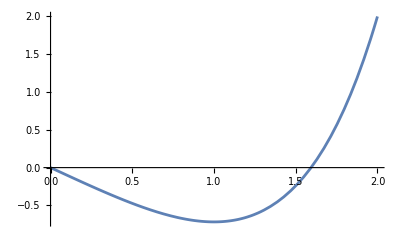

```mathematica
Plot[E^x(x-2)+2,{x,0,2},PlotRange->All]
```

```mathematica
{x^2,(4 x^2 E^-x)/(1-E^-x),(x^2 E^-x)/(1-E^-x),E^-x/(1-E^-x)}/.{x->2+ProductLog[-2/ⅇ^2]}//N
```

{2.53964,2.59044,0.64761,0.255001}

```mathematica
4*0.6476102378919149
```

2.59044

```mathematica
1/1.09
```

0.917431

```mathematica
N[(4γ T(Nbar+1))/(1+Sqrt[κτ Nbar])^2/.{Nbar->5, κτ->2},3]
```

1.39 T γ

```mathematica
κtstar=N[Sqrt[κτ/Nbar]/.{Nbar->5, κτ->2},3]
```

0.632

```mathematica
vals={Nbar->5., κ->1/100.(*us^-1*),τ->200.(*us*),γ->(1/100.)/1000(*us^-1*)};
qfi8=(4(1-η)((2γ+κ)Nbar+γ+κ))/((γ+κ)((1-η)((2γ+κ)Nbar+γ)+κ))/.{η->E^(-κ t)};
snr2=(γ T)/(t+τ)qfi8
snr2N=snr2/.vals
sol=NMaximize[snr2N/T,t]
```

(4 (1-ⅇ^(-t κ)) T γ (γ+κ+Nbar (2 γ+κ)))/((γ+κ) (κ+(1-ⅇ^(-t κ)) (γ+Nbar (2 γ+κ))) (t+τ))

(0.0002402 (1-ⅇ^(-0.01 t)) T)/((0.01+0.05011 (1-ⅇ^(-0.01 t))) (200.+t))

{0.0000127834,{t→58.8653}}

```mathematica
sol[[1]]T
1/sol[[1]]
T/%
snr2N/.sol[[2]]
t/τ/.sol[[2]]/.τ->200.
κ t/.sol[[2]]/.vals
```

0.0000127834 T

78226.2

0.0000127834 T

0.0000127834 T

0.294326

0.588653

```mathematica
Solve[5==snr2N/.sol[[2]],T]
{snr2N/.sol[[2]],T}/.%
Solve[5==Sqrt[snr2N]/.sol[[2]],T]
{snr2N/.sol[[2]],T}/.%
```

{{T→391131.}}

{{5.,391131.}}

{{T→1.95565×10^6}}

{{25.,1.95565×10^6}}

```mathematica
(*check*)
t+τ/.Join[vals,sol[[2]]]
M=7871./%
qfi8/.Join[vals,sol[[2]]]
(γ T)/(t+τ)*%/.Join[vals,sol[[2]]]
(γ T)/(t+τ)/.Join[vals,sol[[2]]]
γ/.vals
1/%
```

258.865

30.4058

330.919

0.0000127834 T

3.86301×10^-8 T

0.00001

100000.

```mathematica
(*high energy limit, in us*)
4/(γ+κ)/.vals
qfi8/(4/(γ+κ))/.Join[vals,sol[[2]]]
```

399.6

0.828125

```mathematica
Limit[qfi8,t->∞]
```

ConditionalExpression[4/(γ+κ), (1/(γ+κ)|γ+2 Nbar γ+Nbar κ)∈ℝ&&κ>0]

```mathematica
(*vacuum*)
vacvals={Nbar->0, κ->1/100.(*us^-1*),τ->200.(*us*),γ->(1/100.)/1000(*us^-1*)};
snr2vac=(γ T)/(t+τ)qfi8
snr2Nvac=snr2vac/.vacvals
solvac=NMaximize[snr2Nvac/T,t]
Sqrt[sol[[1]]/solvac[[1]]]
```

(4 (1-ⅇ^(-t κ)) T γ (γ+κ+Nbar (2 γ+κ)))/((γ+κ) (κ+(1-ⅇ^(-t κ)) (γ+Nbar (2 γ+κ))) (t+τ))

(0.00004 (1-ⅇ^(-0.01 t)) T)/((0.01+0.00001 (1-ⅇ^(-0.01 t))) (200.+t))

{8.87165×10^-6,{t→150.446}}

1.20039

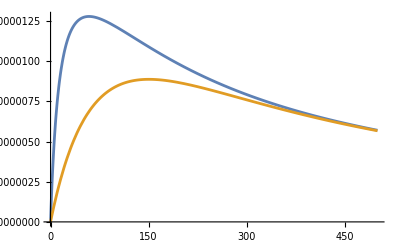

```mathematica
Plot[{snr2N/T,snr2Nvac/T},{t,0,500},PlotRange->All]
```

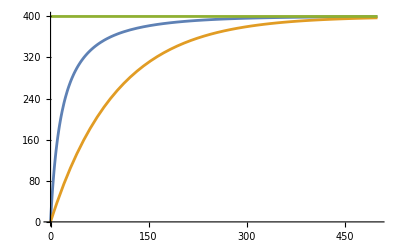

```mathematica
Plot[{qfi8/.vals,qfi8/.vacvals,4/(γ+κ)/.vacvals},{t,0,500},PlotRange->All]
```

```mathematica
vals={Nbar->5., κ->1/100.(*us^-1*),τ->100.(*us*),γ->(1/100.)/1000(*us^-1*)};
qfi8=(4(1-η)((2γ+κ)Nbar+γ+κ))/((γ+κ)((1-η)((2γ+κ)Nbar+γ)+κ))/.{η->E^(-κ t)};
snr2=(γ T)/(t+τ)qfi8
snr2N=snr2/.vals
sol=NMaximize[{snr2N/T,t>0},t]
1/sol[[1]]
Solve[5==Sqrt[snr2N]/.sol[[2]],T]
{snr2N/.sol[[2]],T}/.%
```

(4 (1-ⅇ^(-t κ)) T γ (γ+κ+Nbar (2 γ+κ)))/((γ+κ) (κ+(1-ⅇ^(-t κ)) (γ+Nbar (2 γ+κ))) (t+τ))

(0.0002402 (1-ⅇ^(-0.01 t)) T)/((0.01+0.05011 (1-ⅇ^(-0.01 t))) (100.+t))

{0.000021337,{t→41.0517}}

46866.9

{{T→1.17167×10^6}}

{{25.,1.17167×10^6}}

```mathematica
res=Series[qfi8/.{η->E^(-κ t)},{γ,0,1}]
```

(4 (-1+ⅇ^(t κ)) (1+Nbar))/((ⅇ^(t κ)-Nbar+ⅇ^(t κ) Nbar) κ)-(4 ((-1+ⅇ^(t κ)) (-1+ⅇ^(t κ)-3 Nbar+2 ⅇ^(t κ) Nbar-Nbar^2+ⅇ^(t κ) Nbar^2)) γ)/((ⅇ^(t κ)-Nbar+ⅇ^(t κ) Nbar)^2 κ^2)+O[γ]^2

```mathematica
res=Normal[res]//FullSimplify
```

(4 (-1+ⅇ^(t κ)) (γ+3 Nbar γ+Nbar^2 γ-Nbar κ-Nbar^2 κ+ⅇ^(t κ) (1+Nbar)^2 (-γ+κ)))/((Nbar-ⅇ^(t κ) (1+Nbar))^2 κ^2)

```mathematica
Solve[D[res/(t+τ),t]==0,t]
```

$Aborted

TMSV loss estimation

```mathematica
Σ vac=1/2 IdentityMatrix[4];
Σ TMSV=1/2({{Cosh[2r], 0, Sinh[2r], 0}, {0, Cosh[2r], 0, -Sinh[2r]}, {Sinh[2r], 0, Cosh[2r], 0}, {0, -Sinh[2r], 0, Cosh[2r]}});
```

```mathematica
(*If loss/gain (thermal loss channel) acts only on the first mode*)
Mevo=DiagonalMatrix[{Sqrt[η],Sqrt[η],1,1}];
Nevo=(1-η)(1/2+Subscript[n, th])DiagonalMatrix[{1,1,0,0}];
Σfinal=Mevo.Σ TMSV.Mevoᵀ+Nevo;
```

```mathematica
Σfinal//MatrixForm
```

(1/2 η Cosh[2 r]+(1-η) (1/2+n_th) | 0 | 1/2 √η Sinh[2 r] | 0
0 | 1/2 η Cosh[2 r]+(1-η) (1/2+n_th) | 0 | -1/2 √η Sinh[2 r]
1/2 √η Sinh[2 r] | 0 | 1/2 Cosh[2 r] | 0
0 | -1/2 √η Sinh[2 r] | 0 | 1/2 Cosh[2 r])

```mathematica
μvec=({{0}, {0}, {0}, {0}});
(*loss estimation*)
QFI TMSV=Gaussian QFI Monras13[<|Σ->Σfinal,analytic->True,μvec->μvec,θ->η,print->False,return->True,timeConstrained->True|>]//FullSimplify
```

((1+η-(-1+η) Cosh[2 r]) Sinh[r]^2+2 η Cosh[2 r] n_th)/(η-η^3+(-1+η)^2 η Cosh[2 r] (1+2 n_th))

```mathematica
tmsv1=QFI TMSV/.r->ArcSinh[Sqrt[Nbar]]//FullSimplify
tmsv2=Collect[Numerator[tmsv1],Nbar,FullSimplify]/Collect[Denominator[tmsv1],Nbar,FullSimplify]
tmsv1==tmsv2//FullSimplify
tmsv2==ecqfiUB2//FullSimplify
```

(Nbar (1+Nbar-Nbar η)+(η+2 Nbar η) n_th)/((-1+η) η (-1+Nbar (-1+η)+(1+2 Nbar) (-1+η) n_th))

(Nbar^2 (1-η)+η n_th+Nbar (1+2 η n_th))/(Nbar (-1+η)^2 η (1+2 n_th)+(-1+η) η (-1+(-1+η) n_th))

True

True

```mathematica
(*high energy limit like Tuvia*)
qfiHE=1/2 Tr[MatrixPower[Inverse[Σfinal].D[Σfinal,η],2]]//FullSimplify
```

-(((1+15 η) Cosh[2 r]-2 η (5+3 Cosh[4 r])+(-1+η) Cosh[6 r]+4 Cosh[2 r] n_th (1+7 η+(-1+η) Cosh[4 r]-8 η Cosh[2 r] (1+n_th)))/(8 η (η-(-1+η) Cosh[2 r] (1+2 n_th))^2))

```mathematica
qfiHE1=qfiHE/.r->ArcSinh[Sqrt[Nbar]]//FullSimplify
qfiHE2=Collect[Numerator[qfiHE1],Nbar,FullSimplify]/Collect[Denominator[qfiHE1],Nbar,FullSimplify]
```

(2 Nbar (1+Nbar (3-2 Nbar (-1+η)))+4 (1+2 Nbar) n_th (Nbar (1+Nbar+η-Nbar η)+(η+2 Nbar η) n_th))/(η (-1+2 Nbar (-1+η)+2 (1+2 Nbar) (-1+η) n_th)^2)

(4 η n_th^2-4 Nbar^3 (-1+η) (1+2 n_th)+Nbar (2+4 n_th (1+η+4 η n_th))+Nbar^2 (6+4 n_th (3+η+4 η n_th)))/(4 Nbar^2 (-1+η)^2 η (1+2 n_th)^2+η (1-2 (-1+η) n_th)^2+4 Nbar (-1+η) η (1+2 n_th) (-1+2 (-1+η) n_th))

```mathematica
(-4 Nbar^3 (-1+η) (1+2 Subscript[n, th]))/(4 Nbar^2 (-1+η)^2 η (1+2 Subscript[n, th])^2)
```

-Nbar/((-1+η) η (1+2 n_th))

TMSV generic parameter

```mathematica
(*initial state*)
μvec=({{0}, {0}, {0}, {0}});
Σ vac=1/2 IdentityMatrix[4];
Σ TMSV=1/2({{Cosh[2r], 0, Sinh[2r], 0}, {0, Cosh[2r], 0, -Sinh[2r]}, {Sinh[2r], 0, Cosh[2r], 0}, {0, -Sinh[2r], 0, Cosh[2r]}});
```

```mathematica
(*If loss/gain (thermal loss channel) acts only on the first mode*)
Mevo=DiagonalMatrix[{Sqrt[η[z]],Sqrt[η[z]],1,1}];
Nevo=(1-η[z])(1/2+Subscript[n, th][z])DiagonalMatrix[{1,1,0,0}];
Σfinal=Mevo.Σ TMSV.Mevoᵀ+Nevo;
Σfinal//MatrixForm
```

(1/2 Cosh[2 r] η[z]+(1-η[z]) (1/2+n_th[z]) | 0 | 1/2 Sinh[2 r] √η[z] | 0
0 | 1/2 Cosh[2 r] η[z]+(1-η[z]) (1/2+n_th[z]) | 0 | -1/2 Sinh[2 r] √η[z]
1/2 Sinh[2 r] √η[z] | 0 | 1/2 Cosh[2 r] | 0
0 | -1/2 Sinh[2 r] √η[z] | 0 | 1/2 Cosh[2 r])

```mathematica
(*generic estimation*)
QFI TMSVz=Gaussian QFI Monras13[<|Σ->Σfinal,analytic->True,μvec->μvec,θ->z,print->False,return->True,timeConstrained->True|>]//FullSimplify
```

(n_th[z] (1+n_th[z]) (-1+Cosh[4 r]-8 η[z] (Sinh[r]^4-Cosh[2 r] n_th[z])) η'[z]^2+16 Cosh[2 r] (-1+η[z]) η[z] n_th[z] (1+n_th[z]) η'[z] n_th'[z]+8 (-1+η[z])^2 η[z] (Cosh[r]^2+Cosh[2 r] n_th[z]) n_th'[z]^2)/(8 (-1+η[z]) η[z] n_th[z] (1+n_th[z]) (-Cosh[r]^2+Sinh[r]^2 η[z]+Cosh[2 r] (-1+η[z]) n_th[z]))

```mathematica
(*loss estimation*)
QFI TMSVzloss=QFI TMSVz/.{η[z]->η,η'[z]->1,Subscript[n, th][z]->Subscript[n, th],Subscript[n, th]'[z]->0}//FullSimplify
QFI TMSV loss=Gaussian QFI Monras13[<|Σ->Σfinal,analytic->True,μvec->μvec,θ->η[z],print->False,return->True,timeConstrained->True|>]//FullSimplify;
QFI TMSVzloss==QFI TMSV loss/.{η[z]->η,Subscript[n, th][z]->Subscript[n, th]}//FullSimplify
```

(-1+Cosh[4 r]-8 η Sinh[r]^4+8 η Cosh[2 r] n_th)/(4 (η-η^3+(-1+η)^2 η Cosh[2 r] (1+2 n_th)))

True

```mathematica
(*noise estimation*)
QFI TMSVznoise=QFI TMSVz/.{η[z]->η,η'[z]->0,Subscript[n, th][z]->Subscript[n, th],Subscript[n, th]'[z]->1}//FullSimplify
QFI TMSV noise=Gaussian QFI Monras13[<|Σ->Σfinal,analytic->True,μvec->μvec,θ->Subscript[n, th][z],print->False,return->True,timeConstrained->True|>]//FullSimplify;
QFI TMSVznoise==QFI TMSV noise/.{η[z]->η,Subscript[n, th][z]->Subscript[n, th]}//FullSimplify
```

((-1+η) (Cosh[r]^2+Cosh[2 r] n_th))/(n_th (1+n_th) (-Cosh[r]^2+η Sinh[r]^2+(-1+η) Cosh[2 r] n_th))

True

```mathematica
QFI TMSVzr=QFI TMSVz/.r->ArcSinh[Sqrt[Nbar]]//FullSimplify;
QFI TMSVzr2=Collect[Numerator[QFI TMSVzr],Nbar,FullSimplify]/Collect[Denominator[QFI TMSVzr],Nbar,FullSimplify]
QFI TMSVzr2==QFI TMSVzr//Simplify
```

(-Nbar^2 (-1+η[z]) n_th[z] (1+n_th[z]) η'[z]^2+η[z] (1+n_th[z]) (n_th[z] η'[z]+(-1+η[z]) n_th'[z])^2+Nbar (n_th[z] (1+n_th[z]) (1+2 η[z] n_th[z]) η'[z]^2+4 (-1+η[z]) η[z] n_th[z] (1+n_th[z]) η'[z] n_th'[z]+(-1+η[z])^2 η[z] (1+2 n_th[z]) n_th'[z]^2))/(Nbar (-1+η[z])^2 η[z] n_th[z] (1+n_th[z]) (1+2 n_th[z])+(-1+η[z]) η[z] n_th[z] (1+n_th[z]) (-1+(-1+η[z]) n_th[z]))

True

```mathematica
(*extract coefficients Subscript[c, j] for TMSV and compare to the ECQFI upper bound*)
nlist=CoefficientList[Numerator[QFI TMSVzr2],Nbar];
dlist=CoefficientList[Denominator[QFI TMSVzr2],Nbar];
{c3,c2,c1}=nlist;
{c5,c4}=dlist;
QFI TMSVzr2==(c1 Nbar^2+c2 Nbar+c3)/(c4 Nbar+c5)//FullSimplify
QFI TMSVzrSubList[CL_]:=(CL[[1]] Nbar^2+CL[[2]] Nbar+CL[[3]])/(CL[[4]] Nbar+CL[[5]])
clist={c1,c2,c3,c4,c5};
QFI TMSVzr2==QFI TMSVzrSubList[clist]//FullSimplify
{{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5]},{Nbar^2,Nbar,1,Nbar,1},clist}//Transpose//TableForm
```

True

True

c_1 | Nbar^2 | (1-η[z]) n_th[z] (1+n_th[z]) η'[z]^2
c_2 | Nbar | n_th[z] (1+n_th[z]) (1+2 η[z] n_th[z]) η'[z]^2+4 (-1+η[z]) η[z] n_th[z] (1+n_th[z]) η'[z] n_th'[z]+(-1+η[z])^2 η[z] (1+2 n_th[z]) n_th'[z]^2
c_3 | 1 | η[z] (1+n_th[z]) (n_th[z] η'[z]+(-1+η[z]) n_th'[z])^2
c_4 | Nbar | (-1+η[z])^2 η[z] n_th[z] (1+n_th[z]) (1+2 n_th[z])
c_5 | 1 | (-1+η[z]) η[z] n_th[z] (1+n_th[z]) (-1+(-1+η[z]) n_th[z])

```mathematica
{{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5]},{Nbar^2,Nbar,1,Nbar,1},clist}/.{η[z]->η, Subscript[n, th][z]-> Subscript[n, th],η'[z]->η̇,Subscript[n, th]'[z]->Subscript[ṅ, th]}//Transpose//TableForm
```

c_1 | Nbar^2 | (1-η) (η̇)^2 n_th (1+n_th)
c_2 | Nbar | (η̇)^2 n_th (1+n_th) (1+2 η n_th)+4 (-1+η) η η̇ n_th (1+n_th) (ṅ)_th+(-1+η)^2 η (1+2 n_th) (ṅ)_th^2
c_3 | 1 | η (1+n_th) (η̇ n_th+(-1+η) (ṅ)_th)^2
c_4 | Nbar | (-1+η)^2 η n_th (1+n_th) (1+2 n_th)
c_5 | 1 | (-1+η) η n_th (1+n_th) (-1+(-1+η) n_th)

```mathematica
QFI TMSVzr2/.{η[z]->η, Subscript[n, th][z]-> Subscript[n, th],η'[z]->η̇,Subscript[n, th]'[z]->Subscript[ṅ, th]}
```

(-Nbar^2 (-1+η) (η̇)^2 n_th (1+n_th)+η (1+n_th) (η̇ n_th+(-1+η) (ṅ)_th)^2+Nbar ((η̇)^2 n_th (1+n_th) (1+2 η n_th)+4 (-1+η) η η̇ n_th (1+n_th) (ṅ)_th+(-1+η)^2 η (1+2 n_th) (ṅ)_th^2))/(Nbar (-1+η)^2 η n_th (1+n_th) (1+2 n_th)+(-1+η) η n_th (1+n_th) (-1+(-1+η) n_th))

```mathematica
(*gain estimation, Scenario 1: Γ=G, γ=g=s^2, QFI wrt z=s=Sqrt[γ]*)
gainsubrule={η[z]->E^(-(G-s^2)t),η'[z]->D[E^(-(G-s^2)t),s],Subscript[n, th][z]->s^2/(G-s^2),Subscript[n, th]'[z]->D[s^2/(G-s^2),s]};
QFI TMSVzgain=(QFI TMSVzr2/.gainsubrule)/.s->Sqrt[g]//FullSimplify
```

-((4 (G (G+(g+G) Nbar)+ⅇ^((g-G) t) (-2 G (G+(g+G) Nbar)+2 g (g-G) G (1+2 Nbar) t+g (-g+G)^3 Nbar (1+Nbar) t^2)+ⅇ^(2 (g-G) t) (G (G+(g+G) Nbar)-2 g (g-G) G (1+2 Nbar) t+g (g-G)^2 (-G Nbar^2+g (1+Nbar)^2) t^2)))/((-1+ⅇ^((g-G) t)) (g-G)^2 (G+(g+G) Nbar-ⅇ^((g-G) t) (g+(g+G) Nbar))))

```mathematica
Clear[Γ];
QFI TMSVzgain2=QFI TMSVzgain/.{G->Γ,g->γ};
QFI TMSVzgain3=Collect[Numerator[QFI TMSVzgain2],Nbar,FullSimplify]/Collect[Denominator[QFI TMSVzgain2],Nbar,FullSimplify]
QFI TMSVzgain2==QFI TMSVzgain3//FullSimplify
```

(-4 ⅇ^(t (γ-Γ)) (-1+ⅇ^(t (γ-Γ))) Nbar^2 t^2 γ (γ-Γ)^3-4 (ⅇ^(t (γ-Γ)) (t γ (γ-Γ)-Γ)+Γ)^2-4 Nbar (Γ (γ+Γ)+ⅇ^(2 t (γ-Γ)) (2 t^2 γ^2 (γ-Γ)^2+4 t γ Γ (-γ+Γ)+Γ (γ+Γ))-ⅇ^(t (γ-Γ)) (t^2 γ (γ-Γ)^3+4 t γ Γ (-γ+Γ)+2 Γ (γ+Γ))))/(-(-1+ⅇ^(t (γ-Γ)))^2 Nbar (γ-Γ)^2 (γ+Γ)+(-1+ⅇ^(t (γ-Γ))) (γ-Γ)^2 (-ⅇ^(t (γ-Γ)) γ+Γ))

True

```mathematica
gainsubrule/.{G->Γ,g->γ,s->Sqrt[γ]}//FullSimplify
```

{η[z]→ⅇ^(t (γ-Γ)),η'[z]→2 ⅇ^(t (γ-Γ)) t √γ,n_th[z]→γ/(-γ+Γ),n_th'[z]→(2 √γ Γ)/(γ-Γ)^2}

```mathematica
nlist gain=CoefficientList[Numerator[QFI TMSVzgain2],Nbar]//FullSimplify;
dlist gain=CoefficientList[Denominator[QFI TMSVzgain2],Nbar]//FullSimplify;
{c3 gain,c2 gain,c1 gain}=nlist gain;
{c5 gain,c4 gain}=dlist gain;
QFI TMSVzgain2==(c1 gain Nbar^2+c2 gain Nbar+c3 gain)/(c4 gain Nbar+c5 gain)//FullSimplify
QFI TMSVzrSubList gain[CL_]:=(CL[[1]] Nbar^2+CL[[2]] Nbar+CL[[3]])/(CL[[4]] Nbar+CL[[5]])
clist gain={c1 gain,c2 gain,c3 gain,c4 gain,c5 gain};
QFI TMSVzgain2==QFI TMSVzrSubList gain[clist gain]//FullSimplify
{{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5]},{Nbar^2,Nbar,1,Nbar,1},clist gain}//Transpose//TableForm
```

True

True

c_1 | Nbar^2 | -4 ⅇ^(t (γ-Γ)) (-1+ⅇ^(t (γ-Γ))) t^2 γ (γ-Γ)^3
c_2 | Nbar | -4 Γ (γ+Γ)-4 ⅇ^(2 t (γ-Γ)) (2 t^2 γ^2 (γ-Γ)^2+4 t γ Γ (-γ+Γ)+Γ (γ+Γ))+4 ⅇ^(t (γ-Γ)) (t^2 γ (γ-Γ)^3+4 t γ Γ (-γ+Γ)+2 Γ (γ+Γ))
c_3 | 1 | -4 (ⅇ^(t (γ-Γ)) (t γ (γ-Γ)-Γ)+Γ)^2
c_4 | Nbar | -(-1+ⅇ^(t (γ-Γ)))^2 (γ-Γ)^2 (γ+Γ)
c_5 | 1 | -((-1+ⅇ^(t (γ-Γ))) (γ-Γ)^2 (ⅇ^(t (γ-Γ)) γ-Γ))

```mathematica
QFI TMSVzgain3
```

(-4 ⅇ^(t (γ-Γ)) (-1+ⅇ^(t (γ-Γ))) Nbar^2 t^2 γ (γ-Γ)^3-4 (ⅇ^(t (γ-Γ)) (t γ (γ-Γ)-Γ)+Γ)^2-4 Nbar (Γ (γ+Γ)+ⅇ^(2 t (γ-Γ)) (2 t^2 γ^2 (γ-Γ)^2+4 t γ Γ (-γ+Γ)+Γ (γ+Γ))-ⅇ^(t (γ-Γ)) (t^2 γ (γ-Γ)^3+4 t γ Γ (-γ+Γ)+2 Γ (γ+Γ))))/(-(-1+ⅇ^(t (γ-Γ)))^2 Nbar (γ-Γ)^2 (γ+Γ)+(-1+ⅇ^(t (γ-Γ))) (γ-Γ)^2 (-ⅇ^(t (γ-Γ)) γ+Γ))

```mathematica
(*compare to upper bound on ECQFI from purifications*)
upoptSubStore=-((4 γ (2 ⅇ^(t (γ-Γ)) nbar^2 (γ-Γ) Γ (-ⅇ^(t (γ-Γ)) γ+Γ)^2 (ⅇ^(t (γ-Γ)) (t γ (γ-Γ)-Γ)+Γ) (-1+ⅇ^(t (γ-Γ))+t (-γ+Γ))+1/(ⅇ^(t γ)-ⅇ^(t Γ))ⅇ^(t (γ-2 Γ)) nbar (γ-Γ) Γ (ⅇ^(t γ) γ-ⅇ^(t Γ) Γ)^2 (-1+ⅇ^(t (γ-Γ))+t (-γ+Γ))^2 (-((1+nbar) Γ)+ⅇ^(t (γ-Γ)) (γ+nbar Γ))+1/((-1+ⅇ^(t (γ-Γ))) γ)(-ⅇ^(t (γ-Γ)) γ+Γ)^2 (ⅇ^(t (γ-Γ)) (t γ (γ-Γ)-Γ)+Γ)^2 (ⅇ^(2 t (γ-Γ)) γ ((1+nbar)^2 γ-nbar^2 Γ)+Γ (Γ+nbar (γ+Γ))-ⅇ^(t (γ-Γ)) γ (nbar^2 (γ-Γ)+2 Γ+nbar (γ+3 Γ)))))/((γ-Γ)^2 (-ⅇ^(t (γ-Γ)) γ+Γ)^4 (Γ+nbar (γ+Γ)-ⅇ^(t (γ-Γ)) (γ+nbar γ+nbar Γ))));
QFI TMSVzgain3==upoptSubStore/.nbar->Nbar//FullSimplify 
(*recovers gain estimation!*)
```

True

```mathematica
(c1 gain Nbar^2+c2 gain Nbar+c3 gain)/(c4 gain Nbar+c5 gain)==upoptSubStore/.nbar->Nbar//FullSimplify
```

True

```mathematica
(*proving whether TMSV attains the ECQFI upper bound generically for any generic parameter z encoded in η, Subscript[n, th]*)
uboptStore=(4 Cosh[θ2]^2 OverDot[θ2]^2+4 nbar (Cosh[θ2]^2 OverDot[θ1]^2+Cosh[2 θ2] OverDot[θ2]^2)+4 nbar^2 (Cosh[θ2] OverDot[θ1] Sin[θ1]-Cos[θ1] OverDot[θ2] Sinh[θ2])^2)/(Cosh[θ2]^2+nbar (Cosh[θ2]^2 Sin[θ1]^2+Sinh[θ2]^2));
uboptStore=uboptStore/.nbar->Nbar
```

(4 Cosh[θ2]^2 OverDot[θ2]^2+4 Nbar (Cosh[θ2]^2 OverDot[θ1]^2+Cosh[2 θ2] OverDot[θ2]^2)+4 Nbar^2 (Cosh[θ2] OverDot[θ1] Sin[θ1]-Cos[θ1] OverDot[θ2] Sinh[θ2])^2)/(Cosh[θ2]^2+Nbar (Cosh[θ2]^2 Sin[θ1]^2+Sinh[θ2]^2))

```mathematica
θsToηnRule={θ1->ArcCos[Sqrt[η[z]/(1+(1-η[z])Subscript[n, th][z])]],θ2->ArcCosh[Sqrt[1+(1-η[z])Subscript[n, th][z]]]}
θDotsToηnRule={OverDot[θ1]->D[θ1/.θsToηnRule,z],OverDot[θ2]->D[θ2/.θsToηnRule,z]}//FullSimplify
```

{θ1→ArcCos[√(η[z]/(1+(1-η[z]) n_th[z]))],θ2→ArcCosh[√(1+(1-η[z]) n_th[z])]}

{OverDot[θ1]→(-((1+n_th[z]) η'[z])-(-1+η[z]) η[z] n_th'[z])/(2 √(-((-1+η[z]) η[z] (1+n_th[z]))/(-1+(-1+η[z]) n_th[z])^2) (-1+(-1+η[z]) n_th[z])^2),OverDot[θ2]→(-n_th[z] η'[z]-(-1+η[z]) n_th'[z])/(2 √(1-(-1+η[z]) n_th[z]) √(-1+√(1-(-1+η[z]) n_th[z])) √(1+√(1-(-1+η[z]) n_th[z])))}

```mathematica
addToGlobalAssumptions[{1>η[z]>0,Subscript[n, th][z]>0}]
upopt ηn=(uboptStore/.θDotsToηnRule)/.θsToηnRule//FullSimplify
(*TMSV is generically optimal!*)
upopt ηn==QFI TMSVzr2//FullSimplify
```

(n_th[z] (1+n_th[z]) (Nbar (1+Nbar-Nbar η[z])+(1+2 Nbar) η[z] n_th[z]) η'[z]^2+2 (1+2 Nbar) (-1+η[z]) η[z] n_th[z] (1+n_th[z]) η'[z] n_th'[z]+(-1+η[z])^2 η[z] (1+Nbar+(1+2 Nbar) n_th[z]) n_th'[z]^2)/((-1+η[z]) η[z] n_th[z] (1+n_th[z]) (-1-Nbar+Nbar η[z]+(1+2 Nbar) (-1+η[z]) n_th[z]))

True

SMSV

```mathematica
addToGlobalAssumptions[{γ>0,Γ>0,Γ>γ,t>0,r>0}]
Σ vac=1/2 IdentityMatrix[2];
Σ SMSV=1/2({{Exp[-2r], 0}, {0, Exp[2r]}});
```

```mathematica
Σfinal=η Σ SMSV+(1-η)Σ vac;
Σfinal//MatrixForm
```

((1-η)/2+1/2 ⅇ^(-2 r) η | 0
0 | (1-η)/2+1/2 ⅇ^(2 r) η)

```mathematica
μvec=({{Sqrt[2](2Ω0)/κ(1-Sqrt[η])}, {0}});
```

```mathematica
QFI SMSVdet=Gaussian QFI Monras13[<|Σ->Σfinal,analytic->True,μvec->μvec,θ->Ω0,print->False,return->True,timeConstrained->True|>]//FullSimplify
```

Throw::nocatch: Uncaught Throw[CoB: Dimensions mismatch.] returned to top level.

Hold[Throw[CoB: Dimensions mismatch.]]

```mathematica
QFI=(D[μvec,Ω0]ᵀ.Inverse[Σfinal].D[μvec,Ω0])[[1,1]]//FullSimplify//TrigToExp//Simplify
QFI==(16 (1-√η)^2)/(κ^2(1-η(1-ⅇ^(-2 r)) ))//FullSimplify
```

-(16 ⅇ^(2 r) (-1+√η)^2)/((ⅇ^(2 r) (-1+η)-η) κ^2)

True

```mathematica
ⅇ^(-2 r)-1/.r->ArcSinh[Sqrt[Nbar]]//ExpToTrig//FullSimplify//Factor
```

-2 √Nbar (-√Nbar+√(1+Nbar))

```mathematica
addToGlobalAssumptions[{t>0,κ>0}]
QFIHE=Limit[QFI,r->∞]//FullSimplify
QFIHE/.η->E^(-κ t)//FullSimplify
Series[%,{t,0,2}]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(16 (-1+√η))/((1+√η) κ^2)

(16 Tanh[(t κ)/4])/κ^2

(4 t)/κ+O[t]^3

```mathematica
Series[QFI/.η->E^(-κ t),{t,0,2}]
```

4 ⅇ^(2 r) t^2+O[t]^3

```mathematica
QFI=QFI/.η->E^(-κ t)//FullSimplify
```

(16 ⅇ^(2 r) (-1+ⅇ^((t κ)/2))^2)/((1+ⅇ^(2 r) (-1+ⅇ^(t κ))) κ^2)

```mathematica
addToGlobalAssumptions[{t>0,κ>0,τ>0,r>0}]
ratio=QFI/(t+τ);
Solve[D[ratio,t]==0,t]
```

$Aborted

```mathematica
D[ratio,t]//FullSimplify
```

(16 ⅇ^(2 r) (-1+ⅇ^(2 r)-ⅇ^(2 (r+t κ))+ⅇ^((t κ)/2) (-1+ⅇ^(2 r)) (-2+κ (t+τ))+ⅇ^(2 r+(3 t κ)/2) (2+κ (t+τ))+ⅇ^(t κ) (-1-(-1+2 ⅇ^(2 r)) κ (t+τ))))/((1+ⅇ^(2 r) (-1+ⅇ^(t κ)))^2 κ^2 (t+τ)^2)

```mathematica
QFIhe=Limit[QFI,r->∞]//FullSimplify
QFIhe/(t+τ)
D[QFIhe/(t+τ),t]//FullSimplify
Reduce[D[QFIhe/(t+τ),t]==0]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(16 Tanh[(t κ)/4])/κ^2

(16 Tanh[(t κ)/4])/(κ^2 (t+τ))

(4 Sech[(t κ)/4]^2 (κ (t+τ)-2 Sinh[(t κ)/2]))/(κ^2 (t+τ)^2)

ⅇ^(t κ)==1+ⅇ^((t κ)/2) κ (t+τ)

```mathematica
κ (t+τ)-2 Sinh[(t κ)/2]==0//TrigToExp//Simplify
```

ⅇ^(t κ)==1+ⅇ^((t κ)/2) κ (t+τ)

```mathematica
QFIhe/(2 Sinh[(t κ)/2]/κ)//FullSimplify
```

(4 Sech[(t κ)/4]^2)/κ

```mathematica
TrigReduce[(4 Sech[(t κ)/4]^2)/κ]//FullSimplify
%//TrigReduce
```

(4 Sech[(t κ)/4]^2)/κ

8/(κ (1+Cosh[(t κ)/2]))

```mathematica
Series[Sinh[x],{x,0,5}]
Series[Sin[x],{x,0,5}]
```

x+x^3/6+x^5/120+O[x]^6

x-x^3/6+x^5/120+O[x]^6

```mathematica
κ (t+τ)/2==Normal[Series[Sinh[(t κ)/2],{t,0,3}]]//FullSimplify
Solve[%,t]
```

t^3 κ^2==24 τ

{{t→Root[-24 τ+κ^2 #1^3&,1]}}

```mathematica
Sinh[x]//TrigToExp
```

-ⅇ^-x/2+ⅇ^x/2

```mathematica
(*zero dead time case*)
QFIhe=Limit[QFI,r->∞]//FullSimplify
QFIhe/t
D[QFIhe/t,t]//FullSimplify
Reduce[D[QFIhe/t,t]==0]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(16 Tanh[(t κ)/4])/κ^2

(16 Tanh[(t κ)/4])/(t κ^2)

(4 Sech[(t κ)/4]^2 (t κ-2 Sinh[(t κ)/2]))/(t^2 κ^2)

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[t κ==2 Sinh[(t κ)/2]]

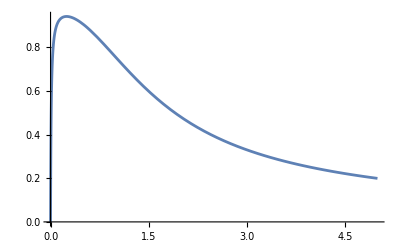

```mathematica
Plot[Tanh[x]/(x+0.01),{x,0,5},PlotRange->All]
```

Coherent expansion, dead time; also gain estimation

```mathematica
FullSimplify[Series[Sech[k t/4]^2/.t->2(3τ/k^2)^(1/3),{τ,0,1}],Assumptions->{k>0,τ>0}]
(4 Ω^2 T)/k Normal[%]
```

1-1/4 (3^(2/3) k^(2/3)) τ^(2/3)+1/8 3^(1/3) k^(4/3) τ^(4/3)+O[τ]^(5/3)

(4 T (1-1/4 3^(2/3) k^(2/3) τ^(2/3)+1/8 3^(1/3) k^(4/3) τ^(4/3)) Ω^2)/k

```mathematica
TrigReduce[Sech[k t/4]^2/.t->2/k Log[k τ]]
(4 Ω^2 T)/k%
```

(4 k τ)/(1+k τ)^2

(16 T τ Ω^2)/(1+k τ)^2

```mathematica
FullSimplify[Series[1/(1+Sqrt[k τ Nbar])^2,{τ,0,1}],Assumptions->{k>0,τ>0}]
```

1-2 √(k Nbar) √τ+3 k Nbar τ+O[τ]^(3/2)

```mathematica
(*short time, gain estimation*)
qfi=(4Nbar γ t)/Γ;
snr2=(γ T qfi)/(t+τ)
```

(4 Nbar t T γ^2)/(Γ (t+τ))

```mathematica
Series[(4 Nbar t T γ^2)/(Γ (t+τ)),{τ,0,1}]//FullSimplify
Normal[%]//FullSimplify
```

(4 Nbar T γ^2)/Γ-(4 (Nbar T γ^2) τ)/(t Γ)+O[τ]^2

(4 Nbar T γ^2 (t-τ))/(t Γ)

```mathematica
D[snr2,t]//FullSimplify
```

(4 Nbar T γ^2 τ)/(Γ (t+τ)^2)

```mathematica
D[t/(t+τ),t]//FullSimplify
```

τ/(t+τ)^2

```mathematica
{t/(t+τ),τ/(t+τ)^2}/.t-> x τ//FullSimplify
```

{x/(1+x),τ/(τ+x τ)^2}

```mathematica
D[x/(1+x),x]//FullSimplify
```

1/(1+x)^2

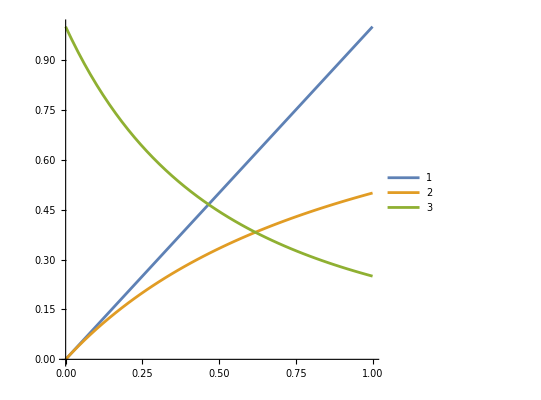

```mathematica
Plot[{x,x/(1+x),1/(1+x)^2},{x,0,1},PlotLegends->Automatic,AspectRatio->1]
```

```mathematica
qfi=4/Γ(1+(Nbar γ t^2 Γ)/(E^(Γ t)-1));
snr2=(γ T)/(t+τ)qfi//Together//FullSimplify
```

(4 T γ (-1+ⅇ^(t Γ)+Nbar t^2 γ Γ))/((-1+ⅇ^(t Γ)) Γ (t+τ))

```mathematica
Reduce[D[snr2,t]==0,t]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-(4 T γ (-1+ⅇ^(t Γ)+Nbar t^2 γ Γ))/((-1+ⅇ^(t Γ)) Γ (t+τ)^2)+(4 T γ (ⅇ^(t Γ) Γ+2 Nbar t γ Γ))/((-1+ⅇ^(t Γ)) Γ (t+τ))-(4 ⅇ^(t Γ) T γ (-1+ⅇ^(t Γ)+Nbar t^2 γ Γ))/((-1+ⅇ^(t Γ))^2 (t+τ))==0,t]

```mathematica
Series[snr2,{t,0,1}]
```

(4 T γ)/(Γ τ)+(4 T γ (-1+Nbar γ τ) t)/(Γ τ^2)+O[t]^2

```mathematica
Series[snr2,{τ,0,1}]//FullSimplify
```

(4 T γ ((Nbar t^2 γ)/(-1+ⅇ^(t Γ))+1/Γ))/t+4 T γ (-(Nbar γ)/(-1+ⅇ^(t Γ))-1/(t^2 Γ)) τ+O[τ]^2

```mathematica
snrx=snr2/.t-> x τ//FullSimplify
```

(4 T γ (-1+ⅇ^(x Γ τ)+Nbar x^2 γ Γ τ^2))/((-1+ⅇ^(x Γ τ)) Γ (τ+x τ))

```mathematica
Series[snrx,{x,0,1}]
```

(4 T γ)/(Γ τ)+(4 T γ (-1+Nbar γ τ) x)/(Γ τ)+O[x]^2

```mathematica
snry=snr2/.τ->y t//FullSimplify
Series[snry,{y,0,1}]
```

(4 T γ (-1+ⅇ^(t Γ)+Nbar t^2 γ Γ))/((-1+ⅇ^(t Γ)) (t+t y) Γ)

(4 T γ (-1+ⅇ^(t Γ)+Nbar t^2 γ Γ))/((-1+ⅇ^(t Γ)) t Γ)-(4 (T γ (-1+ⅇ^(t Γ)+Nbar t^2 γ Γ)) y)/((-1+ⅇ^(t Γ)) t Γ)+O[y]^2

```mathematica
Series[qfi,{t,0,1}]//Normal//FullSimplify
```

(4+4 Nbar t γ)/Γ

```mathematica
(*chatgpt's trick*)
Series[x^2/((x+δ)(E^x-1)),{δ,0,1},{x,0,1}]//Normal//FullSimplify//Expand
Series[x^2/((x+δ)(E^x-1)),{x,0,3},{δ,0,2}]//Normal//FullSimplify//Expand
```

1-x/2+δ/2-δ/x-(x δ)/12

x^3/δ^3-x^2/δ^2+x^3/(2 δ^2)+x/δ-x^2/(2 δ)+x^3/(12 δ)

```mathematica
sol=Solve[D[1-x/2+δ/2-δ/x,x]==0,x]
1-x/2+δ/2-δ/x/.sol
%/.δ->Γ τ
```

{{x→-√2 √δ},{x→√2 √δ}}

{1+√2 √δ+δ/2,1-√2 √δ+δ/2}

{1+(Γ τ)/2+√2 √(Γ τ),1+(Γ τ)/2-√2 √(Γ τ)}

```mathematica
Series[x^2/(E^x-1),{x,0,2}]
```

x-x^2/2+O[x]^3

```mathematica
Series[(Sqrt[2y]-y)/(Sqrt[2y]+y),{y,0,1}]
```

1-√2 √y+y+O[y]^(3/2)

End matter

```mathematica
c1=4γ t^2(Γ-γ)^3 η(1-η);
c2=4Γ(Γ+γ)+4 η^2(
Γ(Γ+γ)+2 γ^2 t^2(Γ-γ)^2+4γ Γ t(Γ-γ)
)-4η(
2Γ(Γ+γ)-γ t^2(Γ-γ)^3+4γ Γ t(Γ-γ)
);
c3=4(Γ-η(Γ+γ t(Γ-γ)))^2;
c4=(Γ-γ)^2(Γ+γ)(1-η)^2;
c5=(Γ-γ)^2(1-η)(Γ-γ η);
```

```mathematica
(*Eq.14*)
Limit[(c1 Nbar^2+c2 Nbar+c3)/(c4 Nbar+c5),γ->0]//FullSimplify
```

(4 (1+Nbar) (-1+η))/(Γ (-1+Nbar (-1+η)))

```mathematica
(*Eq.15*)
(c1 Nbar)/c4
```

(4 Nbar t^2 γ (-γ+Γ) η)/((γ+Γ) (1-η))

Long interrogation time limit

```mathematica
p[n_]:=x^n/(1+x)^(n+1)
Sum[D[p[n],x]^2/p[n],{n,0,∞}]
D[σ^2/(Γ-σ^2),σ]^2 Sum[D[p[n],x]^2/p[n],{n,0,∞}]/.x->σ^2/(Γ-σ^2)//FullSimplify
```

1/(x (1+x))

(4 Γ)/((Γ-σ^2)^2)

```mathematica
(4 Ns)/(1+Nb)1/(1+Ns/(1+Ns)Nb/(1+Nb))//FullSimplify
Numerator[%]/Collect[Denominator[%],Ns]
```

(4 Ns (1+Ns))/(1+Nb+Ns+2 Nb Ns)

(4 Ns (1+Ns))/(1+Nb+(1+2 Nb) Ns)

```mathematica
1/(nth(1+nth))D[s^2/(G-s^2),s]^2/.nth->s^2/(G-s^2)//FullSimplify
```

(4 G)/((G-s^2)^2)

```mathematica
(x+q  l^2 y)/(1+q l)^2(y+q x)/(x y)-1//FullSimplify
```

(q (x-l y)^2)/((1+l q)^2 x y)

```mathematica
(x+q  l^2 y)(y+q x)-(1+q l)^2 x y//FullSimplify
```

q (x-l y)^2

```mathematica
FullSimplify[Minimize[(Nb+q l^2(Nb+1))/(1+q l)^2,l],Assumptions->{Nb>=0,q>=0}]
```

{(Nb (1+Nb))/(1+Nb+Nb q),{l→Piecewise[{{Nb/(1+Nb), q>0}, {0, True}}]}}

Stochastic signal models

```mathematica
FullSimplify[(4 Subscript[Ω, 0]^2)/κ^2(1-Sqrt[η])/(1+Sqrt[η])/.η->E^(-κ t),Assumptions->{κ>0,t>0}]
Series[%,{t,0,4}]
Series[Tanh[x],{x,0,4}]
```

(4 Ω_0^2 Tanh[(t κ)/4])/κ^2

(Ω_0^2 t)/κ-1/48 (κ Ω_0^2) t^3+O[t]^5

x-x^3/3+O[x]^5

```mathematica
FullSimplify[(4 Subscript[Ω, 0]^2)/κ^2(1-Sqrt[η])^2/.η->E^(-κ t),Assumptions->{κ>0,t>0}]
FullSimplify[((4 Subscript[Ω, 0]^2)/κ^2(1-Sqrt[η])^2)/(1-η)/.η->E^(-κ t),Assumptions->{κ>0,t>0}]
```

(4 (-1+ⅇ^(-(t κ)/2))^2 Ω_0^2)/κ^2

(4 Ω_0^2 Tanh[(t κ)/4])/κ^2

```mathematica
addToGlobalAssumptions[{κ>0,Element[ϕ,Reals]}]
```

```mathematica
α=-I Integrate[E^(-κ(t-s)/2)Ω[s],{s,0,t}]
```

-ⅈ ∫_0^t ⅇ^(-1/2 (-s+t) κ) Ω[s]ⅆs

```mathematica
α/.Ω[s]:>Subscript[Ω, 0] E^(I ϕ)//FullSimplify
```

-(2 ⅈ ⅇ^(-(t κ)/2+ⅈ ϕ) (-1+ⅇ^((t κ)/2)) Ω_0)/κ

```mathematica
α/.Ω[s]:>Subscript[Ω, 0] E^(I ω s+I ϕ)//FullSimplify
```

(2 ⅇ^(-(t κ)/2+ⅈ ϕ) (-1+ⅇ^(1/2 t (κ+2 ⅈ ω))) Ω_0)/(ⅈ κ-2 ω)

```mathematica
D[(2 ⅇ^(-(t κ)/2+ⅈ ϕ) (-1+ⅇ^(1/2 t (κ+2 ⅈ ω))) Subscript[Ω, 0])/(ⅈ κ-2 ω),t]//FullSimplify
```

(ⅇ^(-(t κ)/2+ⅈ ϕ) (κ+2 ⅈ ⅇ^(1/2 t (κ+2 ⅈ ω)) ω) Ω_0)/(ⅈ κ-2 ω)

```mathematica
addToGlobalAssumptions[{κ>0,Γϕ>0}] 
Integrate[ Integrate[E^(κ(s+s2)/2)E^(-Γϕ Abs[s-s2]),{s2,0,t}],{s,0,t}]
```

∫_0^t (∫_0^t ⅇ^(1/2 (s+s2) κ-Γϕ Abs[s-s2])ⅆs2)ⅆs

```mathematica
p1=Integrate[Integrate[E^(κ(s+s2)/2)E^(-Γϕ (s-s2)),{s2,0,s}],{s,0,t}]//FullSimplify
p2=Integrate[Integrate[E^(κ(s+s2)/2)E^(-Γϕ (s2-s)),{s2,s,t}],{s,0,t}]//FullSimplify
p1+p2//FullSimplify
E^(-κ t)(p1+p2)//FullSimplify
```

(-4 (-1+ⅇ^(t κ)) Γϕ+2 (1+ⅇ^(t κ)-2 ⅇ^(1/2 t (-2 Γϕ+κ))) κ)/(-4 Γϕ^2 κ+κ^3)

(-4 (-1+ⅇ^(t κ)) Γϕ+2 (1+ⅇ^(t κ)-2 ⅇ^(1/2 t (-2 Γϕ+κ))) κ)/(-4 Γϕ^2 κ+κ^3)

(-8 (-1+ⅇ^(t κ)) Γϕ+4 (1+ⅇ^(t κ)-2 ⅇ^(1/2 t (-2 Γϕ+κ))) κ)/(-4 Γϕ^2 κ+κ^3)

(4 ⅇ^(-t κ) (-2 (-1+ⅇ^(t κ)) Γϕ+(1+ⅇ^(t κ)-2 ⅇ^(1/2 t (-2 Γϕ+κ))) κ))/(-4 Γϕ^2 κ+κ^3)

```mathematica
FullSimplify[ComplexExpand[Abs[E^(I w t)-Sqrt[η]]],Assumptions->η>0]
FullSimplify[ComplexExpand[Abs[E^(I w t)-Sqrt[η]]],Assumptions->{η>0,w t==π}]
```

√(1+η-2 √η Cos[t w])

1+√η

```mathematica
v=Ω0^2 E^(-κ t)(-4 (-1+ⅇ^(t κ)) Γϕ+2 (1+ⅇ^(t κ)-2 ⅇ^(1/2 t (-2 Γϕ+κ))) κ)/(-4 Γϕ^2 κ+κ^3);
Series[v,{t,0,2}]
```

(Ω0^2 t^2)/2+O[t]^3

```mathematica
Series[v,{Γϕ,0,1}]//ExpToTrig//FullSimplify
```

(8 ⅇ^(-(t κ)/2) Ω0^2 Sinh[(t κ)/4]^2)/κ^2-(4 (ⅇ^(-t κ) (-1+ⅇ^(t κ)-ⅇ^((t κ)/2) t κ) Ω0^2) Γϕ)/κ^3+O[Γϕ]^2

```mathematica
Series[v,{κ,0,1}]//FullSimplify
```

((-1+ⅇ^(-t Γϕ)+t Γϕ) Ω0^2)/Γϕ^2-((ⅇ^(-t Γϕ) t (1+ⅇ^(t Γϕ) (-1+t Γϕ)) Ω0^2) κ)/(2 Γϕ^2)+O[κ]^2

```mathematica
redo={t->x/κ,Γϕ->(κ/2)/y,Ω0->κ z};
undo={x->κ t,y->(κ/2)/Γϕ,z->Ω0/κ};
v=2 Ω0^2 E^(-κ t)(-4 (-1+ⅇ^(t κ)) Γϕ+2 (1+ⅇ^(t κ)-2 ⅇ^(1/2 t (-2 Γϕ+κ))) κ)/(-4 Γϕ^2 κ+κ^3);
vv=v/.redo//FullSimplify
v==vv/.undo//FullSimplify
```

(4 ⅇ^-x y (1+ⅇ^x (-1+y)+y-2 ⅇ^((x (-1+y))/(2 y)) y) z^2)/(-1+y^2)

True

```mathematica
(* y = ( κ/2 )/Γϕ << 1 *)
vv1=Series[vv,{y,0,1}]//FullSimplify
vv1=Normal[vv1]/.undo//FullSimplify
vv1//ExpandAll
```

ⅇ^(-x/(2 y)+x/2+O[y]^2) O[y]^2+(4 ⅇ^-x (-1+ⅇ^x) z^2 y+O[y]^2)

(2 Ω0^2-2 ⅇ^(-t κ) Ω0^2)/(Γϕ κ)

(2 Ω0^2)/(Γϕ κ)-(2 ⅇ^(-t κ) Ω0^2)/(Γϕ κ)

```mathematica
vv2=Series[vv,{y,0,2}]//FullSimplify
vv2=Normal[vv2]/.undo//FullSimplify
vv2//ExpandAll
```

ⅇ^(-x/(2 y)+x/2+O[y]^3) (8 ⅇ^-x z^2 y^2+O[y]^3)+(4 ⅇ^-x (-1+ⅇ^x) z^2 y-4 (ⅇ^-x (1+ⅇ^x) z^2) y^2+O[y]^3)

-(ⅇ^(-t (Γϕ+κ)) (-2 ⅇ^((t κ)/2) κ+ⅇ^(t (Γϕ+κ)) (-2 Γϕ+κ)+ⅇ^(t Γϕ) (2 Γϕ+κ)) Ω0^2)/(Γϕ^2 κ)

-Ω0^2/Γϕ^2-(ⅇ^(-t κ) Ω0^2)/Γϕ^2+(2 ⅇ^(-t Γϕ-(t κ)/2) Ω0^2)/Γϕ^2+(2 Ω0^2)/(Γϕ κ)-(2 ⅇ^(-t κ) Ω0^2)/(Γϕ κ)

```mathematica
vv2/vv1//FullSimplify
%==1+κ/(2Γϕ)(1+ⅇ^(t κ)-2 ⅇ^(-t Γϕ+(t κ)/2))/(1-ⅇ^(t κ))//FullSimplify
```

1+(κ+ⅇ^(t κ) κ-2 ⅇ^(-t Γϕ+(t κ)/2) κ)/(2 Γϕ-2 ⅇ^(t κ) Γϕ)

True

```mathematica
Series[(1+ⅇ^(t κ)-2 ⅇ^(-t Γϕ+(t κ)/2))/(1-ⅇ^(t κ)),{t,0,2}]
Series[vv2/vv1,{t,0,2}]
```

-(2 Γϕ)/κ+((4 Γϕ^2-κ^2) t)/(4 κ)+((-4 Γϕ^3+Γϕ κ^2) t^2)/(12 κ)+O[t]^3

((4 Γϕ^2-κ^2) t)/(8 Γϕ)+1/24 (-4 Γϕ^2+κ^2) t^2+O[t]^3

```mathematica
vv2/vv1/.redo//FullSimplify
Series[vv2/vv1/.redo,{y,0,1}]//Normal//FullSimplify
Series[vv2/vv1,{t,0,1}]//Normal//FullSimplify
```

-(1+ⅇ^x (-1+y)+y-2 ⅇ^((x (-1+y))/(2 y)) y)/(-1+ⅇ^x)

1+(2 ⅇ^((x (-1+y))/(2 y)) y)/(-1+ⅇ^x)

t (Γϕ/2-κ^2/(8 Γϕ))

```mathematica
v
```

(2 ⅇ^(-t κ) (-4 (-1+ⅇ^(t κ)) Γϕ+2 (1+ⅇ^(t κ)-2 ⅇ^(1/2 t (-2 Γϕ+κ))) κ) Ω0^2)/(-4 Γϕ^2 κ+κ^3)

```mathematica
Series[vv1,{t,0,1}]
```

(2 Ω0^2 t)/Γϕ+O[t]^2

```mathematica
Series[vv2,{t,0,2}]
```

((4 Γϕ^2-κ^2) Ω0^2 t^2)/(4 Γϕ^2)+O[t]^3

```mathematica
rule1={t->x/κ,Γϕ->(κ/2)/y,Ω0->κ z};
v=2 Ω0^2 E^(-κ t)(-4 (-1+ⅇ^(t κ)) Γϕ+2 (1+ⅇ^(t κ)-2 ⅇ^(1/2 t (-2 Γϕ+κ))) κ)/(-4 Γϕ^2 κ+κ^3);
vR=v/.{t->w/Γϕ}//FullSimplify
Series[vR,{w,0,2}]
```

(4 ⅇ^(-(w κ)/Γϕ) (-2 (-1+ⅇ^((w κ)/Γϕ)) Γϕ+(1+ⅇ^((w κ)/Γϕ)-2 ⅇ^(1/2 w (-2+κ/Γϕ))) κ) Ω0^2)/(-4 Γϕ^2 κ+κ^3)

(Ω0^2 w^2)/Γϕ^2+O[w]^3

```mathematica
Limit[v,κ->0]//FullSimplify//Expand
Series[%,{t,0,2}]
Series[%%,{Γϕ,0,1}]
```

-(2 Ω0^2)/Γϕ^2+(2 ⅇ^(-t Γϕ) Ω0^2)/Γϕ^2+(2 t Ω0^2)/Γϕ

Ω0^2 t^2+O[t]^3

t^2 Ω0^2-1/3 (t^3 Ω0^2) Γϕ+O[Γϕ]^2

```mathematica
v//ExpandAll
vg=(8 Γϕ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)-(8 ⅇ^(t κ) Γϕ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)+(4 κ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)+(4 ⅇ^(t κ) κ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)-(8 ⅇ^((t κ)/2) κ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3) ⅇ^(-t Γϕ);
vg==v//Simplify
```

(8 Γϕ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)-(8 ⅇ^(t κ) Γϕ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)+(4 κ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)+(4 ⅇ^(t κ) κ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)-(8 ⅇ^(-t Γϕ+(t κ)/2) κ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)

True

```mathematica
vgg=(8 Γϕ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)-(8 ⅇ^(t κ) Γϕ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)+(4 κ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)+(4 ⅇ^(t κ) κ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3)-(8 ⅇ^((t κ)/2) κ Ω0^2)/(-4 ⅇ^(t κ) Γϕ^2 κ+ⅇ^(t κ) κ^3) ⅇ^(-1/s);
v==vgg/.s->1/(t Γϕ)//Simplify
(*s=1/t Γϕ;*)
```

True

```mathematica
Series[vgg,{s,0,1}]//Normal//FullSimplify
vG=Limit[vgg,{s->∞}]//FullSimplify
%//Expand
```

-(4 ⅇ^(-t κ) (2 (-1+ⅇ^(t κ)) Γϕ+(-1-ⅇ^(t κ)+2 ⅇ^(-1/s+(t κ)/2)) κ) Ω0^2)/(-4 Γϕ^2 κ+κ^3)

(4 ⅇ^(-t κ) (-2 (-1+ⅇ^(t κ)) Γϕ+(-1+ⅇ^((t κ)/2))^2 κ) Ω0^2)/(-4 Γϕ^2 κ+κ^3)

-(8 Γϕ Ω0^2)/(-4 Γϕ^2 κ+κ^3)+(8 ⅇ^(-t κ) Γϕ Ω0^2)/(-4 Γϕ^2 κ+κ^3)+(4 κ Ω0^2)/(-4 Γϕ^2 κ+κ^3)+(4 ⅇ^(-t κ) κ Ω0^2)/(-4 Γϕ^2 κ+κ^3)-(8 ⅇ^(-(t κ)/2) κ Ω0^2)/(-4 Γϕ^2 κ+κ^3)

```mathematica
redo
undo
vgr=vG/.redo//FullSimplify
```

{t→x/κ,Γϕ→κ/(2 y),Ω0→z κ}

{x→t κ,y→κ/(2 Γϕ),z→Ω0/κ}

(4 ⅇ^-x y (1+ⅇ^x (-1+y)+y-2 ⅇ^(x/2) y) z^2)/(-1+y^2)

```mathematica
Normal[Series[vgr,{y,0,1}]]/.undo//FullSimplify
```

(2 Ω0^2-2 ⅇ^(-t κ) Ω0^2)/(Γϕ κ)

```mathematica
vv2//ExpandAll
vv2g=-Ω0^2/Γϕ^2-(ⅇ^(-t κ) Ω0^2)/Γϕ^2+(2 Ω0^2)/(Γϕ κ)-(2 ⅇ^(-t κ) Ω0^2)/(Γϕ κ)//FullSimplify
%//ExpandAll
```

-Ω0^2/Γϕ^2-(ⅇ^(-t κ) Ω0^2)/Γϕ^2+(2 ⅇ^(-t Γϕ-(t κ)/2) Ω0^2)/Γϕ^2+(2 Ω0^2)/(Γϕ κ)-(2 ⅇ^(-t κ) Ω0^2)/(Γϕ κ)

-(ⅇ^(-t κ) (2 Γϕ+κ+ⅇ^(t κ) (-2 Γϕ+κ)) Ω0^2)/(Γϕ^2 κ)

-Ω0^2/Γϕ^2-(ⅇ^(-t κ) Ω0^2)/Γϕ^2+(2 Ω0^2)/(Γϕ κ)-(2 ⅇ^(-t κ) Ω0^2)/(Γϕ κ)

```mathematica
(-Ω0^2/Γϕ^2-(ⅇ^(-t κ) Ω0^2)/Γϕ^2)/((2 Ω0^2)/(Γϕ κ)-(2 ⅇ^(-t κ) Ω0^2)/(Γϕ κ))//FullSimplify
```

-(κ Coth[(t κ)/2])/(2 Γϕ)

```mathematica
Coth[x]//TrigToExp
Series[Coth[x],{x,0,1}]
```

(ⅇ^-x+ⅇ^x)/(-ⅇ^-x+ⅇ^x)

1/x+x/3+O[x]^2

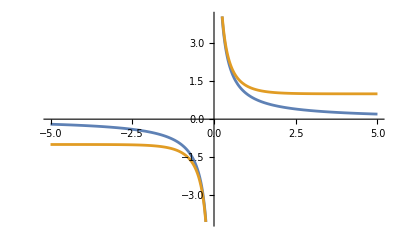

```mathematica
Plot[{1/x,Coth[x]},{x,-5,5}]
```

```mathematica
(*vv2/vv1*)
1+(κ+ⅇ^(t κ) κ)/(2 Γϕ-2 ⅇ^(t κ) Γϕ)//FullSimplify
```

1-(κ Coth[(t κ)/2])/(2 Γϕ)

```mathematica
v=Ω^2/(k/2+G)((1-E^(-k t))/(k/2)+(2 E^(-k t))/(k/2-G))//FullSimplify
```

(4 (ⅇ^(-k t)/(-2 G+k)+1/(2 G+k)) Ω^2)/k

```mathematica
Series[v,{k,0,1}]
```

(2 (-1+G t) Ω^2)/G^2+((t-G t^2) Ω^2 k)/G^2+O[k]^2

```mathematica
V=Ω^2/(k/2+G)((1-η)/(k/2)+(2η)/(k/2-G))//FullSimplify
Series[V,{k,0,1}]
```

(4 (k+2 G (-1+η)+k η) Ω^2)/(-4 G^2 k+k^3)

-(2 ((-1+η) Ω^2))/(G k)-((1+η) Ω^2)/G^2-(((-1+η) Ω^2) k)/(2 G^3)+O[k]^2

```mathematica
(-((1+η) Ω^2)/G^2)/(-(2 ((-1+η) Ω^2))/(G k))//FullSimplify
%/.η->E^(-k t)//FullSimplify
```

(k (1+η))/(2 G (-1+η))

-(k Coth[(k t)/2])/(2 G)

Asymmetric TMSV

```mathematica
(*initial state*)
μvec=({{0}, {0}, {0}, {0}});
Σ vac=1/2 IdentityMatrix[4];
(*Subscript[x, 1],Subscript[p, 1],Subscript[x, 2],Subscript[p, 2] form*)
Σ TMSV=1/2({{Cosh[2r], 0, Sinh[2r], 0}, {0, Cosh[2r], 0, -Sinh[2r]}, {Sinh[2r], 0, Cosh[2r], 0}, {0, -Sinh[2r], 0, Cosh[2r]}});
```

```mathematica
(*If loss/gain (thermal loss channel) acts only on the first mode*)
Mevo=DiagonalMatrix[{Sqrt[η],Sqrt[η],1,1}];
Nevo=DiagonalMatrix[{(1-η)1/2,(1-η)1/2+σ^2,0,0}];
Σfinal=Mevo.Σ TMSV.Mevoᵀ+Nevo;
Σfinal//MatrixForm
```

((1-η)/2+1/2 η Cosh[2 r] | 0 | 1/2 √η Sinh[2 r] | 0
0 | (1-η)/2+σ^2+1/2 η Cosh[2 r] | 0 | -1/2 √η Sinh[2 r]
1/2 √η Sinh[2 r] | 0 | 1/2 Cosh[2 r] | 0
0 | -1/2 √η Sinh[2 r] | 0 | 1/2 Cosh[2 r])

```mathematica
(*asymmetric noise estimation*)
QFI TMSVz=Gaussian QFI Monras13[<|Σ->Σfinal,analytic->True,μvec->μvec,θ->σ,print->False,return->True,timeConstrained->True|>]//FullSimplify
```

(-5+7 η-7 η^2+5 η^3+14 σ^2-28 η σ^2+30 η^2 σ^2-4 (-1+η) η (-1+η+13 σ^2) Cosh[2 r]-4 (-1+η-η^2+η^3-4 (1+2 (-1+η) η) σ^2) Cosh[4 r]+4 (-1+η) η (-1+η-3 σ^2) Cosh[6 r]-(-1+η)^2 (-1+η-2 σ^2) Cosh[8 r])/((3-2 η+3 η^2-3 (-1+η) σ^2+4 η (1-η+σ^2) Cosh[2 r]+(-1+η) (-1+η-σ^2) Cosh[4 r]) (4 η (1-η+σ^2) Cosh[2 r]+(-1+η) (1+3 η-2 σ^2+(-1+η-2 σ^2) Cosh[4 r])))

```mathematica
QFI TMSVzN=QFI TMSVz/.r->ArcSinh[Sqrt[Nbar]]//TrigExpand//FullSimplify;
Limit[QFI TMSVzN,Nbar->∞]//FullSimplify
QFI TMSVzN2=Collect[Numerator[QFI TMSVzN],Nbar,FullSimplify]/Collect[Denominator[QFI TMSVzN],Nbar,FullSimplify]
QFI TMSVzN==QFI TMSVzN2//FullSimplify
```

2/(1-η+σ^2)

(2 σ^2-8 Nbar^4 (-1+η)^2 (-1+η-2 σ^2)-4 Nbar (-1+η+(-3+η) σ^2)+4 Nbar^2 (3+2 η^2+7 σ^2-5 η (1+σ^2))-8 Nbar^3 (-1+η) (2+η^2+4 σ^2-η (3+σ^2)))/(σ^2+σ^4+4 Nbar^4 (-1+η)^2 (-1+η-2 σ^2) (-1+η-σ^2)-4 Nbar^3 (-1+η) (-1+η-σ^2) (2 (-1+η)+(-4+η) σ^2)+Nbar^2 (6 (-1+η)^2+4 (-1+η) (-5+2 η) σ^2+2 (7-5 η) σ^4)+Nbar (2+8 σ^2+6 σ^4-2 η (1+3 σ^2+σ^4)))

True

```mathematica
(*single-mode squeezing applied to TMSV*)
Mevo2=DiagonalMatrix[{Exp[s],Exp[-s],1,1}];
Nevo2=DiagonalMatrix[{0,0,0,0}];
Σ TMSV2=Mevo2.Σ TMSV.Mevo2ᵀ+Nevo2;
Σ TMSV2//MatrixForm
Σfinal=Mevo.Σ TMSV2.Mevoᵀ+Nevo;
Σfinal//MatrixForm
```

(1/2 ⅇ^(2 s) Cosh[2 r] | 0 | 1/2 ⅇ^s Sinh[2 r] | 0
0 | 1/2 ⅇ^(-2 s) Cosh[2 r] | 0 | -1/2 ⅇ^-s Sinh[2 r]
1/2 ⅇ^s Sinh[2 r] | 0 | 1/2 Cosh[2 r] | 0
0 | -1/2 ⅇ^-s Sinh[2 r] | 0 | 1/2 Cosh[2 r])

((1-η)/2+1/2 ⅇ^(2 s) η Cosh[2 r] | 0 | 1/2 ⅇ^s √η Sinh[2 r] | 0
0 | (1-η)/2+σ^2+1/2 ⅇ^(-2 s) η Cosh[2 r] | 0 | -1/2 ⅇ^-s √η Sinh[2 r]
1/2 ⅇ^s √η Sinh[2 r] | 0 | 1/2 Cosh[2 r] | 0
0 | -1/2 ⅇ^-s √η Sinh[2 r] | 0 | 1/2 Cosh[2 r])

```mathematica
(*QFI of the asymmetric TMSV state*)
QFI TMSV2z=Gaussian QFI Monras13[<|Σ->Σfinal,analytic->True,μvec->μvec,θ->σ,print->False,return->True,timeConstrained->True|>]//FullSimplify
```

(ⅇ^(-4 s) (32 ⅇ^(8 s) η^2 σ^2 Cosh[2 r]^2+4 ⅇ^(6 s) (-1+η) η Cosh[2 r] (1-η-10 σ^2+(-1+η-6 σ^2) Cosh[4 r])+ⅇ^(4 s) (-1+η) (5-2 η+5 η^2+14 (-1+η) σ^2-4 (1+η^2-4 (-1+η) σ^2) Cosh[4 r]-(-1+η) (-1+η-2 σ^2) Cosh[8 r])+4 ⅇ^(2 s) (-1+η)^2 η Sinh[2 r] Sinh[4 r]))/((3-2 η+3 η^2-3 (-1+η) σ^2+(-1+η-σ^2) ((-1+η) Cosh[4 r]-4 η Cosh[2 r] Cosh[2 s])+4 η σ^2 Cosh[2 r] Sinh[2 s]) ((-1+η) (1+3 η-2 σ^2)+(-1+η) (-1+η-2 σ^2) Cosh[4 r]+4 η Cosh[2 r] ((1-η+σ^2) Cosh[2 s]+σ^2 Sinh[2 s])))

```mathematica
Limit[QFI TMSV2z,r->∞]
```

2/(1-η+σ^2)

```mathematica
QFI TMSVz==Limit[QFI TMSV2z,s->0]//FullSimplify
```

True

```mathematica
(*average photon number in the probe/signal mode*)
(Σ TMSV2[[1,1]]+Σ TMSV2[[2,2]]-1)/2//FullSimplify
Limit[%,s->0]//FullSimplify
(*average photon number in the ancilla/idler mode*)
(Σ TMSV2[[3,3]]+Σ TMSV2[[4,4]]-1)/2//FullSimplify
```

1/2 (-1+Cosh[2 r] Cosh[2 s])

Sinh[r]^2

Sinh[r]^2

Export formulae to Python for plotting

```mathematica
toPythonTranslation = {η->eta,σ->sigma};
```

```mathematica
Module[{path,nb},
path="/home/james/Code/pleasantpheasant/mathematica/ExportToPython.nb";
nb=NotebookOpen[path,CellContext->"Global`",Visible->False];
NotebookEvaluate[nb,InsertResults->False];
NotebookClose[nb];
];
Export[dir<>"../python_source/_QFI_asymmetric_TMSV_raw.py",QFI TMSV2z//TrigToExp//#/.toPythonTranslation&//ToPython,"Text"];
```